## Read shell

```mathematica
(********************* FILE PATH *******************************)
SetDirectory[NotebookDirectory[]];
(****************** Load shell structure *****************************)
ecubicOrigin=Import["../../../Cpp/ecubic_89396.dat","Integer32"];
eshellMax=89397;
ecubic=Table[ecubicOrigin⟦147(i-1)+j⟧,{i,1,eshellMax},{j,1,147}];
(****************** Load shell structure *****************************)
```

```mathematica
(****************** Load shell structure *****************************)
cubic=Import["cubic_expansion_10k.txt","Table"];
(* cubic中每个shell的前三个数: (1)模长, (2)shellType (0~6), (3)shellNum *)
(****************** Load shell structure *****************************)
```

```mathematica
(****************** Load shell structure *****************************)
cubic001=Import["cubic_001_expansion_28719.txt","Table"];
(* cubic001中每个shell的前四个数: (1)|n.d|, (2)n^2, (3)shellNum (4)无用的run_Index *)
(****************** Load shell structure *****************************)
```

```mathematica
(****************** Load shell structure *****************************)
cubic110=Import["cubic_110_expansion_27304.txt","Table"];
(* cubic011中每个shell的前四个数: (1)|n.d|, (2)n^2, (3)shellNum (4)无用的run_Index *)
(****************** Load shell structure *****************************)
```

```mathematica
readoutShell[i_]:=Module[{vecIdx={4,5,6},vecnum,shell,vi},
vecnum=ecubic⟦i,2⟧;
shell={};
For[vi=1,vi≤vecnum,vi++,shell=Append[shell,ecubic⟦i,3(vi-1)+vecIdx⟧]];
shell]
```

## O_h - group element (necessary codes)

```mathematica
(*****************************************************************)
(*            Subscript[n, 1] Subscript[n, 2] Subscript[n, 3]   ω      ψ    θ     ϕ                                     *)
cubeElement={{0, 0, 1, 0, 0, 0, 0}, {1/√3, 1/√3, 1/√3, -2π/3, -π/2, -π/2, 0}, {1/√3, 1/√3, 1/√3, 2π/3, 0, π/2, π/2}, {-1/√3, 1/√3, 1/√3, -2π/3, 0, -π/2, -π/2}, {-1/√3, 1/√3, 1/√3, 2π/3, π/2, π/2, 0}, {-1/√3, -1/√3, 1/√3, -2π/3, -π/2, π/2, 0}, {-1/√3, -1/√3, 1/√3, 2π/3, 0, -π/2, π/2}, {1/√3, -1/√3, 1/√3, -2π/3, 0, π/2, -π/2}, {1/√3, -1/√3, 1/√3, 2π/3, π/2, -π/2, 0}, {1, 0, 0, -π/2, -π/2, -π/2, π/2}, {1, 0, 0, π/2, π/2, -π/2, -π/2}, {0, 1, 0, -π/2, 0, -π/2, 0}, {0, 1, 0, π/2, 0, π/2, 0}, {0, 0, 1, -π/2, -π/2, 0, 0}, {0, 0, 1, π/2, π/2, 0, 0}, {0, 1/√2, 1/√2, -π, -π/2, -π/2, -π/2}, {0, -1/√2, 1/√2, -π, -π/2, π/2, -π/2}, {1/√2, 1/√2, 0, -π, -π/2, -π, 0}, {1/√2, -1/√2, 0, -π, 0, π, -π/2}, {1/√2, 0, 1/√2, -π, 0, π/2, -π}, {-1/√2, 0, 1/√2, -π, 0, -π/2, -π}, {1, 0, 0, -π, π, π, 0}, {0, 1, 0, -π, 0, -π, 0}, {0, 0, 1, -π, 0, 0, -π}};
(*****************************************************************)
(* Rotation in real space is equivalent to Subscript[T, 1]*)
RT1[i_]:=Module[{M1,M2,M3,ω,result},
M1=Table[If[α==β,1,0],{α,1,3},{β,1,3}];
M2=Table[cubeElement⟦i,α⟧cubeElement⟦i,β⟧,{α,1,3},{β,1,3}];
M3=Table[Sum[LeviCivitaTensor[3]⟦α,β,k⟧cubeElement⟦i,k⟧,{k,1,3}],{α,1,3},{β,1,3}];
ω=cubeElement⟦i,4⟧;
result=(Cos[ω]M1+(1-Cos[ω])M2-Sin[ω]M3);
result];
(*****************************************************************)
(* 48 rotations by multiplying reflection *)
rot=Join[RT1[#]&/@Range[24],-RT1[#]&/@Range[24]];
(*****************************************************************)
```

## Group matrix in irreps

```mathematica
RA1[i_]:={{1}};
RA1a[i_]:=If[i≥25,RA1[i-24],RA1[i]];
RA1b[i_]:=If[i≥25,-RA1[i-24],RA1[i]];
RA2[i_]:=If[i≥10&&i≤21,{{-1}},{{1}}];
RA2a[i_]:=If[i≥25,RA2[i-24],RA2[i]];
RA2b[i_]:=If[i≥25,-RA2[i-24],RA2[i]];

RE[i_]:=If[i==1||i==22||i==23||i==24,
{{1,0},{0,1}},If[i==14||i==15||i==18||i==19,
{{1,0},{0,-1}},If[i==2||i==5||i==6||i==9,
{{-Cos[π/3],Sin[π/3]},{-Sin[π/3],-Cos[π/3]}},If[i==3||i==4||i==7||i==8,
{{-Cos[π/3],-Sin[π/3]},{Sin[π/3],-Cos[π/3]}},If[i==10||i==11||i==16||i==17,
{{-Cos[π/3],-Sin[π/3]},{-Sin[π/3],Cos[π/3]}},
{{-Cos[π/3],Sin[π/3]},{Sin[π/3],Cos[π/3]}}
]
]
]
]
];
REa[i_]:=If[i≥25,RE[i-24],RE[i]];
REb[i_]:=If[i≥25,-RE[i-24],RE[i]];

RT1a[i_]:=If[i≥25,RT1[i-24],RT1[i]];
RT1b[i_]:=If[i≥25,-RT1[i-24],RT1[i]];

RT2[i_]:=If[i≥10&&i≤21,-RT1[i],RT1[i]];
RT2a[i_]:=If[i≥25,RT2[i-24],RT2[i]];
RT2b[i_]:=If[i≥25,-RT2[i-24],RT2[i]];

DimIrreps[irreps_]:=If[irreps=="A1+"||irreps=="A1-"||irreps=="A2+"||irreps=="A2-",1,If[irreps=="E+"||irreps=="E-",2,3]];
GroupMatrix[i_,irreps_]:=If[irreps=="A1+",RA1a[i],If[irreps=="A1-",RA1b[i],If[irreps=="A2+",RA2a[i],If[irreps=="A2-",RA2b[i],If[irreps=="E+",REa[i],If[irreps=="E-",REb[i],If[irreps=="T1+",RT1a[i],If[irreps=="T1-",RT1b[i],If[irreps=="T2+",RT2a[i],RT2b[i]]]]]]]]]];
```

## Rebuild the shell data

```mathematica
RebuildShell[i0_,ii_,preSet_]:=Module[{i,vec1st,vecRef,shellLen,shellType,shellNum,NewShell,j,cubicX},
cubicX=preSet;

For[i=i0,i≤ii,i++,
vec1st=ecubic⟦i,#⟧&/@{4,5,6};
vecRef=Sort@Abs@vec1st;

shellLen=vecRef.vecRef;
If[vecRef⟦1⟧==0&&vecRef⟦2⟧==0&&vecRef⟦3⟧==0,shellType=0,If[vecRef⟦1⟧==0&&vecRef⟦2⟧==0,shellType=1,If[vecRef⟦1⟧==0&&vecRef⟦2⟧==vecRef⟦3⟧,shellType=2,If[vecRef⟦1⟧==0,shellType=3,If[vecRef⟦1⟧==vecRef⟦2⟧&&vecRef⟦2⟧==vecRef⟦3⟧,shellType=4,If[vecRef⟦1⟧==vecRef⟦2⟧||vecRef⟦2⟧==vecRef⟦3⟧,shellType=5,shellType=6]]]]]];
If[shellType==0,shellNum=1,If[shellType==1,shellNum=6,If[shellType==2,shellNum=12,If[shellType==3,shellNum=24,If[shellType==4,shellNum=8,If[shellType==5,shellNum=24,shellNum=48]]]]]];

NewShell={{shellLen,shellType,shellNum}};

For[j=1,j≤48,j++,AppendTo[NewShell,rot⟦j⟧.vecRef]];

AppendTo[cubicX,Flatten@NewShell];
];
cubicX];
```

```mathematica
cubic0={Table[If[i==3,1,0],{i,1,147}]}
cubic1=RebuildShell[2,200,cubic0];
```

{{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
(*[n^2] [type of shell] [# or shell] [nx] [ny] [nz] [nx] [ny] [nz] ... *)
```

Type of shell: 
(000) → type 0
(00a) → type 1
(0a a)→type 2
(0a b)→type 3
(a a a)→type 4
(a b b)→type 5
(a b c)→type 6

```mathematica
Export["cubic_expansion.txt",cubic1,"Table","FieldSeparators"->" "];
```

```mathematica
cubic0=Import["cubic_expansion.txt","Table"];
i0=Length@cubic0+1;
ii=10000;
cubic1=RebuildShell[i0,ii,cubic0];
```

```mathematica
Export["cubic_expansion_10k.txt",cubic1,"Table","FieldSeparators"->" "];
```

## Irreps in shell

```mathematica
irrepsInShell={{"A1+"},{"A1+","E+","T1-"},{"A1+","E+","T1-","T2+","T2-"},{"A1+","A2+"
,"E+","T1+","T1-","T2+","T2-"},{"A1+","A2-","T1-","T2+"},{"A1+","A2-","E+","E-","T1+","T1-","T2+","T2-"},{"A1+","A1-","A2+","A2-","E+","E-","T1+","T1-","T2+","T2-"}};
irrepsContribute[shell_,irreps_]:=If[MemberQ[irrepsInShell⟦cubic⟦shell,2⟧+1⟧,irreps],1,0];
```

```mathematica
vecRef={0,0,0};
irrepsSet={"A1+","A1-","A2+","A2-","E+","E-","T1+","T1-","T2+","T2-"};
ContributeJudge[shellVec_,irreps_]:=Module[{Vtest,sum,result},
Vtest[p_,q_]:=1/((p-vecRef/√7).q+q.q+(p-vecRef/√7).(p-vecRef/√7)+1);
sum=Sum[Vtest[rot⟦i⟧.shellVec,shellVec]GroupMatrix[i,irreps],{i,1,Length@rot}];
result=If[sum==DiagonalMatrix[Table[0,{i,1,DimIrreps[irreps]}]],False,True];
(*result=If[MemberQ[{"E+","E-"},irreps],If[sum==DiagonalMatrix[{0,0}],False,True],If[MemberQ[{"T1+","T1-","T2+","T2-"},irreps],If[sum==DiagonalMatrix[{0,0,0}],False,True],If[sum=={{0}},False,True]]];*)
result];
ContributeJudgeSum[shellVec_,irreps_]:=Module[{Vtest,sum,result},
Vtest[p_,q_]:=1/((p-vecRef/√7).q+q.q+(p-vecRef/√7).(p-vecRef/√7)+1);
sum=Sum[Vtest[rot⟦i⟧.shellVec,shellVec]GroupMatrix[i,irreps],{i,1,Length@rot}];
result=If[sum==DiagonalMatrix[Table[0,{i,1,DimIrreps[irreps]}]],False,True];
(*result=If[MemberQ[{"E+","E-"},irreps],If[sum==DiagonalMatrix[{0,0}],False,True],If[MemberQ[{"T1+","T1-","T2+","T2-"},irreps],If[sum==DiagonalMatrix[{0,0,0}],False,True],If[sum=={{0}},False,True]]];*)
{result,sum}];
```

```mathematica
itest=1;
ptest=cubic⟦itest,#⟧&/@{4,5,6};
Print["reference: ",ptest,". shellnum: ",cubic⟦itest,3⟧];
checknum=0;
For[i=1,i≤Length@irrepsSet,i++,
resss=ContributeJudgeSum[ptest,irrepsSet⟦i⟧];
If[resss⟦1⟧,{multisss=If[DimIrreps[irrepsSet⟦i⟧]>1,DimIrreps[irrepsSet⟦i⟧]-Count[FullSimplify@Eigenvalues@resss⟦2⟧,0],1];Print[irrepsSet⟦i⟧,": True(",multisss,")."];checknum+=DimIrreps[irrepsSet⟦i⟧]multisss;},{Print[irrepsSet⟦i⟧,": False."]}]
];
If[checknum==cubic⟦itest,3⟧,Print["check OK!"],Print["check num goes wrong!"]];
```

reference: {0,0,0}. shellnum: 1

A1+: True(1).

A1-: False.

A2+: False.

A2-: False.

E+: False.

E-: False.

T1+: False.

T1-: False.

T2+: False.

T2-: False.

check OK!

```mathematica
itest=2;
ptest=cubic⟦itest,#⟧&/@{4,5,6};
Print["reference: ",ptest,". shellnum: ",cubic⟦itest,3⟧];
checknum=0;
For[i=1,i≤Length@irrepsSet,i++,
resss=ContributeJudgeSum[ptest,irrepsSet⟦i⟧];
If[resss⟦1⟧,{multisss=If[DimIrreps[irrepsSet⟦i⟧]>1,DimIrreps[irrepsSet⟦i⟧]-Count[FullSimplify@Eigenvalues@resss⟦2⟧,0],1];Print[irrepsSet⟦i⟧,": True(",multisss,")."];checknum+=DimIrreps[irrepsSet⟦i⟧]multisss;},{Print[irrepsSet⟦i⟧,": False."]}]
];
If[checknum==cubic⟦itest,3⟧,Print["check OK!"],Print["check num goes wrong!"]];
```

reference: {0,0,1}. shellnum: 6

A1+: True(1).

A1-: False.

A2+: False.

A2-: False.

E+: True(1).

E-: False.

T1+: False.

T1-: True(1).

T2+: False.

T2-: False.

check OK!

```mathematica
itest=3;
ptest=cubic⟦itest,#⟧&/@{4,5,6};
Print["reference: ",ptest,". shellnum: ",cubic⟦itest,3⟧];
checknum=0;
For[i=1,i≤Length@irrepsSet,i++,
resss=ContributeJudgeSum[ptest,irrepsSet⟦i⟧];
If[resss⟦1⟧,{multisss=If[DimIrreps[irrepsSet⟦i⟧]>1,DimIrreps[irrepsSet⟦i⟧]-Count[FullSimplify@Eigenvalues@resss⟦2⟧,0],1];Print[irrepsSet⟦i⟧,": True(",multisss,")."];checknum+=DimIrreps[irrepsSet⟦i⟧]multisss;},{Print[irrepsSet⟦i⟧,": False."]}]
];
If[checknum==cubic⟦itest,3⟧,Print["check OK!"],Print["check num goes wrong!"]];
```

reference: {0,1,1}. shellnum: 12

A1+: True(1).

A1-: False.

A2+: False.

A2-: False.

E+: True(1).

E-: False.

T1+: False.

T1-: True(1).

T2+: True(1).

T2-: True(1).

check OK!

```mathematica
itest=4;
ptest=cubic⟦itest,#⟧&/@{4,5,6};
Print["reference: ",ptest,". shellnum: ",cubic⟦itest,3⟧];
checknum=0;
For[i=1,i≤Length@irrepsSet,i++,
resss=ContributeJudgeSum[ptest,irrepsSet⟦i⟧];
If[resss⟦1⟧,{multisss=If[DimIrreps[irrepsSet⟦i⟧]>1,DimIrreps[irrepsSet⟦i⟧]-Count[FullSimplify@Eigenvalues@resss⟦2⟧,0],1];Print[irrepsSet⟦i⟧,": True(",multisss,")."];checknum+=DimIrreps[irrepsSet⟦i⟧]multisss;},{Print[irrepsSet⟦i⟧,": False."]}]
];
If[checknum==cubic⟦itest,3⟧,Print["check OK!"],Print["check num goes wrong!"]];
```

reference: {1,1,1}. shellnum: 8

A1+: True(1).

A1-: False.

A2+: False.

A2-: True(1).

E+: False.

E-: False.

T1+: False.

T1-: True(1).

T2+: True(1).

T2-: False.

check OK!

```mathematica
itest=6;
ptest=cubic⟦itest,#⟧&/@{4,5,6};
Print["reference: ",ptest,". shellnum: ",cubic⟦itest,3⟧];
checknum=0;
For[i=1,i≤Length@irrepsSet,i++,
resss=ContributeJudgeSum[ptest,irrepsSet⟦i⟧];
If[resss⟦1⟧,{multisss=If[DimIrreps[irrepsSet⟦i⟧]>1,DimIrreps[irrepsSet⟦i⟧]-Count[FullSimplify@Eigenvalues@resss⟦2⟧,0],1];Print[irrepsSet⟦i⟧,": True(",multisss,")."];checknum+=DimIrreps[irrepsSet⟦i⟧]multisss;},{Print[irrepsSet⟦i⟧,": False."]}]
];
If[checknum==cubic⟦itest,3⟧,Print["check OK!"],Print["check num goes wrong!"]];
```

reference: {0,1,2}. shellnum: 24

A1+: True(1).

A1-: False.

A2+: True(1).

A2-: False.

E+: True(2).

E-: False.

T1+: True(1).

T1-: True(2).

T2+: True(1).

T2-: True(2).

check OK!

```mathematica
itest=7;
ptest=cubic⟦itest,#⟧&/@{4,5,6};
Print["reference: ",ptest,". shellnum: ",cubic⟦itest,3⟧];
checknum=0;
For[i=1,i≤Length@irrepsSet,i++,
resss=ContributeJudgeSum[ptest,irrepsSet⟦i⟧];
If[resss⟦1⟧,{multisss=If[DimIrreps[irrepsSet⟦i⟧]>1,DimIrreps[irrepsSet⟦i⟧]-Count[FullSimplify@Eigenvalues@resss⟦2⟧,0],1];Print[irrepsSet⟦i⟧,": True(",multisss,")."];checknum+=DimIrreps[irrepsSet⟦i⟧]multisss;},{Print[irrepsSet⟦i⟧,": False."]}]
];
If[checknum==cubic⟦itest,3⟧,Print["check OK!"],Print["check num goes wrong!"]];
```

reference: {1,1,2}. shellnum: 24

A1+: True(1).

A1-: False.

A2+: False.

A2-: True(1).

E+: True(1).

E-: True(1).

T1+: True(1).

T1-: True(2).

T2+: True(2).

T2-: True(1).

check OK!

```mathematica
itest=15;
ptest=cubic⟦itest,#⟧&/@{4,5,6};
Print["reference: ",ptest,". shellnum: ",cubic⟦itest,3⟧];
checknum=0;
For[i=1,i≤Length@irrepsSet,i++,
resss=ContributeJudgeSum[ptest,irrepsSet⟦i⟧];
If[resss⟦1⟧,{multisss=If[DimIrreps[irrepsSet⟦i⟧]>1,DimIrreps[irrepsSet⟦i⟧]-Count[FullSimplify@Eigenvalues@resss⟦2⟧,0],1];Print[irrepsSet⟦i⟧,": True(",multisss,")."];checknum+=DimIrreps[irrepsSet⟦i⟧]multisss;},{Print[irrepsSet⟦i⟧,": False."]}]
];
If[checknum==cubic⟦itest,3⟧,Print["check OK!"],Print["check num goes wrong!"]];
```

reference: {1,2,3}. shellnum: 48

A1+: True(1).

A1-: True(1).

A2+: True(1).

A2-: True(1).

E+: True(2).

E-: True(2).

T1+: True(3).

T1-: True(3).

T2+: True(3).

T2-: True(3).

check OK!

## Kinematic term and Potential (necessary codes)

```mathematica
mN=1;mπ=140/938;mρ=770/938;L=2π;g=101/100;V0=mπ^2/mN;
ω[p_,P_]:=((2π)/L)^2((p-P/2).(p-P/2))/mN;
Vg[p_,q_]:=g^2/((2π/L)^2(p-q).(p-q)+mπ^2);
VSF[p_,q_]:=(-4π g)(1/(mN mρ))Sinc[√((p-q).(p-q))/mρ]+(-4π V0)(2mπ)/(((2π/L)^2(p-q).(p-q)+mπ^2)^2);
V[p_,q_]:=Vg[p,q];
```

(x P+p)^2/(2 m_1) +(y P-p)^2/(2 m_2)=P^2/(2(m_1+m_2))+p^2/(2μ)

其中, x=m_1/(m_1+m_2),y=m_2/(m_1+m_2); 即,p_1=m_1/(m_1+m_2)P, p_2=m_2/(m_1+m_2)P
换言之,总动量 P=p_1+p_2, 相对动量 p=y p_1 - x p_2 = μ(v_1 - v_2) = μ (p_1/m_1 - p_2/m_2)=p_1- (m_1 P)/(m_1+m_2);
相对动量是伽利略变换不变量, 因为相对速度是不变量. 于是, 相对动能 p^2/(2μ) 也是不变量.

```mathematica
mN=1;mNp=3/2;mπ=140/938;mρ=770/938;L=2π;g=101/100;V0=mπ^2/mN;xx:=mN/(mN+mNp);yy:=mNp/(mN+mNp);μ:=(mN mNp)/(mN+mNp);
ω[p_,P_]:=((2π)/L)^2((p-xx P).(p-xx P))/(2μ);
Vg[p_,q_]:=g^2/((2π/L)^2(p-q).(p-q)+mπ^2);
VSF[p_,q_]:=(-4π g)(1/(mN mρ))Sinc[√((p-q).(p-q))/mρ]+(-4π V0)(2mπ)/(((2π/L)^2(p-q).(p-q)+mπ^2)^2);
V[p_,q_]:=VSF[p,q];
```

## no Projection

```mathematica
Ematrix[pbegin_,pcut_]:=Module[{i,ii,p,element,Ediag,Emtr},
Ediag={};
For[i=pbegin,i≤pcut,i++,
p=ecubic⟦i,#⟧&/@{4,5,6};
element=ω[p];
For[ii=1,ii≤ecubic⟦i,2⟧,ii++,
AppendTo[Ediag,element];
];
];
Emtr=DiagonalMatrix[Ediag];
Emtr];
Vmatrix[pbegin_,pcut_]:=Module[{i,ii,p,pIndex,j,jj,q,qIndex,Vmtr,currentRow,element},
pIndex=0;
qIndex=0;
Vmtr={};
For[i=pbegin,i≤pcut,i++,
For[ii=1,ii≤ecubic⟦i,2⟧,ii++,
p=ecubic⟦i,#⟧&/@(3ii+{1,2,3});
pIndex++;
(*Print[pIndex,"): ",p];*)
currentRow={};
For[j=pbegin,j≤1pcut,j++,
For[jj=1,jj≤ecubic⟦j,2⟧,jj++,
q=ecubic⟦j,#⟧&/@(3jj+{1,2,3});
qIndex++;
(*Print[qIndex,"): ",q];*)
element=If[pIndex>qIndex,Vmtr⟦qIndex,pIndex⟧,(1/L)^3 V[p,q]];
AppendTo[currentRow,element];
];
];
AppendTo[Vmtr,currentRow];
];
];
Vmtr];
EnergyLevels[pbegin_,pcut_]:=Module[{Emtr,Vmtr,Hmtr,result0,result},
Emtr=Ematrix[pbegin,pcut];
Vmtr=Vmatrix[pbegin,pcut];
Hmtr=Emtr+Vmtr;
result0=Eigenvalues[SetPrecision[Hmtr,prec]];
result=Sort@DeleteDuplicates[result0];
For[i=1,i≤Length@result,i++,Print[result⟦i⟧]];
result];
```

```mathematica
g=100/100;mπ=1;
(*Ematrix[1,3]//MatrixForm
Vmatrix[1,3]//MatrixForm*)
EnergyLevels[1,5];
```

0.00399313106315883

1.00214881492064

1.00214881492064

1.00321591833228

1.00321591833228

1.00321591833228

1.01009784315939

2.00204771647195

2.00204771647195

2.00204771647195

2.00225307842536

2.00225307842536

2.0028644921057

2.0028644921057

2.0028644921057

2.00511415040884

2.00511415040884

2.00511415040884

2.01378285788057

3.00264627974837

3.00308963732807

3.00308963732807

3.00308963732807

3.00408945905105

3.00408945905105

3.00408945905105

3.00819279845788

4.0033734065519

4.0033734065519

4.00379889627837

4.00379889627837

4.00379889627837

4.00611325950287

## Projection

```mathematica
EmatrixProjection[pbegin_,pcut_,irreps_]:=Module[{i,ii,p,element,Ediag,Emtr},
Ediag={};
For[i=pbegin,i≤pcut,i++,
If[irrepsContribute[i,irreps]==1,
{p=cubic⟦i,#⟧&/@{4,5,6};
element=ω[p];
For[ii=1,ii≤DimIrreps[irreps],ii++,
AppendTo[Ediag,element];
];
}];
];
Emtr=If[Length@Ediag==0,{{}},DiagonalMatrix[Ediag]];
Emtr];

VmatrixProjection[pbegin_,pcut_,irreps_]:=Module[{i,ii,p,pnum,pIndex,iIndex,j,jj,q,qnum,qIndex,jIndex,Vmtr0,Vmtr,dim,zeroMtr,elementMtr,gi},
pIndex=0;
qIndex=0;
Vmtr0=Table[0,{i,1,1000},{j,1,1000}];
dim=DimIrreps[irreps];
zeroMtr=Table[0,{i,1,dim},{j,1,dim}];
For[j=pbegin,j≤pcut,j++,
If[irrepsContribute[j,irreps]==1,
{q=cubic⟦j,#⟧&/@{4,5,6};
qnum=cubic⟦j,3⟧;
qIndex++;
pIndex=0;
(*Print["[q] ",qIndex,"): ",q];*)
For[i=pbegin,i≤pcut,i++,
If[irrepsContribute[i,irreps]==1,
{elementMtr=zeroMtr;
pnum=cubic⟦i,3⟧;
pIndex++;
For[gi=1,gi≤48,gi++,
p=cubic⟦i,#⟧&/@(3gi+{1,2,3});
elementMtr+=Conjugate@Transpose@(GroupMatrix[gi,irreps]V[p,q]);
];
(*Print["[p] ",pIndex,"): ",MatrixForm@elementMtr];*)
For[ii=1,ii≤dim,ii++,
For[jj=1,jj≤dim,jj++,
iIndex=(pIndex-1)*dim+ii;
jIndex=(qIndex-1)*dim+jj;
Vmtr0⟦iIndex,jIndex⟧=((√(pnum qnum))/48)(1/L^3)elementMtr⟦ii,jj⟧;
]
];
}];
];
}];
];
Vmtr=If[pIndex==0,{{}},Table[Vmtr0⟦i,j⟧,{i,1,pIndex dim},{j,1,qIndex dim}]];
Vmtr];
EnergyLevelsProjection[pbegin_,pcut_,irreps_]:=Module[{Emtr,Vmtr,Hmtr,result0,result},
Emtr=EmatrixProjection[pbegin,pcut,irreps];
Vmtr=VmatrixProjection[pbegin,pcut,irreps];
Hmtr=Emtr+Vmtr;
If[Hmtr=={{}},{result={};Print[{}]},{result0=Eigenvalues[SetPrecision[Hmtr,prec]];
result=Sort@Select[result0,Abs[Round[#]-#]≥10^-9&];
For[i=1,i≤Length@result,i++,Print[result⟦i⟧]]}];
result];
```

```mathematica
g=100/100;mπ=1;
(*EmatrixProjection[1,5,"A1+"]//MatrixForm
VmatrixProjection[1,5,"A1+"]//MatrixForm*)
EnergyLevelsProjection[1,5,"A1+"];
```

0.00399313106315883

1.01009784315939

2.01378285788057

3.00819279845788

4.00611325950287

```mathematica
g=100/100;mπ=1;
(*EmatrixProjection[1,5,"E+"]//MatrixForm
VmatrixProjection[1,5,"E+"]//MatrixForm*)
EnergyLevelsProjection[1,5,"E+"];
```

1.

1.00214881492064

2.

2.00225307842536

4.

4.0033734065519

## Calculation

### Set 1

```mathematica
g=101/100;mπ=140/938;p0=1;pf=6;prec=16;
```

```mathematica
(*Ematrix[p0,pf]//MatrixForm
Vmatrix[p0,pf]//MatrixForm*)
EnergyLevels[p0,pf];
```

0.184480350058398

1.18155153950194

1.18353509511981

1.19346490084321

2.18139115344041

2.18173637604108

2.18305436851129

2.18676455943808

2.19800332365576

3.18273749914532

3.18342901529757

3.18481482500532

3.18972389956097

4.18380209259037

4.18430751583573

4.1868531814877

5.18068267747105

5.18108303669757

5.18170647979347

5.18209413855595

5.18285765111377

5.18377589766088

5.18498566486623

5.18662381787244

5.18999258102572

5.19966709486603

___________________________________
0 →(000): A_1^+
1 →(001): A_1^+ E^+ T_1^-
2 →(011): A_1^+ E^+ T_1^- T_2^+ T_2^-
3 →(111): A_1^+ A_2^- T_1^- T_2^+
4 →(002): A_1^+ E^+ T_1^-
5 →(012): A_1^+ A_2^+ E^+ E^+ T_1^+ T_1^- T_1^- T_2^+ T_2^- T_2^-
___________________________________

```mathematica
irreps="A1+";
(*EmatrixProjection[p0,pf,irreps]//MatrixForm
Simplify@VmatrixProjection[p0,pf,irreps]//MatrixForm*)
EnergyLevelsProjection[p0,pf,irreps];
```

0.184480350058398

1.19346490084321

2.19800332365576

3.18972389956097

4.1868531814877

5.19966709486603

```mathematica
irreps="A1-";
(*EmatrixProjection[p0,pf,irreps]//MatrixForm
Simplify@VmatrixProjection[p0,pf,irreps]//MatrixForm*)
EnergyLevelsProjection[p0,pf,irreps];
```

{}

```mathematica
irreps="A2+";
(*EmatrixProjection[p0,pf,irreps]//MatrixForm
Simplify@VmatrixProjection[p0,pf,irreps]//MatrixForm*)
EnergyLevelsProjection[p0,pf,irreps];
```

5.18068267747105

```mathematica
irreps="A2-";
(*EmatrixProjection[p0,pf,irreps]//MatrixForm
Simplify@VmatrixProjection[p0,pf,irreps]//MatrixForm*)
EnergyLevelsProjection[p0,pf,irreps];
```

3.18273749914532

```mathematica
irreps="E+";
(*EmatrixProjection[p0,pf,irreps]//MatrixForm
Simplify@VmatrixProjection[p0,pf,irreps]//MatrixForm*)
EnergyLevelsProjection[p0,pf,irreps];
```

1.1815515395019

2.1817363760411

4.1838020925904

5.1817064797935

5.1866238178724

```mathematica
irreps="E-";
(*EmatrixProjection[p0,pf,irreps]//MatrixForm
Simplify@VmatrixProjection[p0,pf,irreps]//MatrixForm*)
EnergyLevelsProjection[p0,pf,irreps];
```

{}

```mathematica
irreps="T1+";
(*EmatrixProjection[p0,pf,irreps]//MatrixForm
Simplify@VmatrixProjection[p0,pf,irreps]//MatrixForm*)
EnergyLevelsProjection[p0,pf,irreps];
```

5.18209413855595

```mathematica
irreps="T1-";
(*EmatrixProjection[p0,pf,irreps]//MatrixForm
Simplify@VmatrixProjection[p0,pf,irreps]//MatrixForm*)
EnergyLevelsProjection[p0,pf,irreps];
```

1.18353509511981

2.18676455943808

3.18481482500532

4.18430751583573

5.18285765111377

5.18999258102572

```mathematica
irreps="T2+";
(*EmatrixProjection[p0,pf,irreps]//MatrixForm
Simplify@VmatrixProjection[p0,pf,irreps]//MatrixForm*)
EnergyLevelsProjection[p0,pf,irreps];
```

2.18305436851129

3.18342901529757

5.18498566486623

```mathematica
irreps="T2-";
(*EmatrixProjection[p0,pf,irreps]//MatrixForm
Simplify@VmatrixProjection[p0,pf,irreps]//MatrixForm*)
EnergyLevelsProjection[p0,pf,irreps];
```

2.18139115344041

5.18108303669757

5.18377589766088

### Set 2 (VSF)

```mathematica
V[p_,q_]:=VSF[p,q];p0=1;pf=6;prec=16;
```

```mathematica
(*Ematrix[p0,pf]//MatrixForm
Vmatrix[p0,pf]//MatrixForm*)
EnergyLevels[p0,pf];
```

-0.77651305733561

0.055644881724145

0.26016355407163

0.31333472799483

1.1194534240984

1.1681227816724

1.2956601576159

1.3083524133716

1.318488616894

2.2249895714146

2.2602007839183

2.2822415468375

2.3118439786349

3.242278545388

3.2511794768652

3.2985558009173

4.1286333395629

4.1785388468755

4.2277149249083

4.2882827398322

4.2932028926335

4.3016230537339

4.3173996042479

4.3181712930111

4.3209736348546

4.321317384577

___________________________________
0 →(000): A_1^+
1 →(001): A_1^+ E^+ T_1^-
2 →(011): A_1^+ E^+ T_1^- T_2^+ T_2^-
3 →(111): A_1^+ A_2^- T_1^- T_2^+
4 →(002): A_1^+ E^+ T_1^-
5 →(012): A_1^+ A_2^+ E^+ E^+ T_1^+ T_1^- T_1^- T_2^+ T_2^- T_2^-
___________________________________

```mathematica
irreps="A1+";
(*EmatrixProjection[p0,pf,irreps]//MatrixForm
Simplify@VmatrixProjection[p0,pf,irreps]//MatrixForm*)
EnergyLevelsProjection[p0,pf,irreps];
```

-0.77651305733561

0.055644881724145

1.1194534240984

2.2602007839183

3.2985558009173

4.2932028926335

```mathematica
irreps="A1-";
(*EmatrixProjection[p0,pf,irreps]//MatrixForm
Simplify@VmatrixProjection[p0,pf,irreps]//MatrixForm*)
EnergyLevelsProjection[p0,pf,irreps];
```

{}

```mathematica
irreps="A2+";
(*EmatrixProjection[p0,pf,irreps]//MatrixForm
Simplify@VmatrixProjection[p0,pf,irreps]//MatrixForm*)
EnergyLevelsProjection[p0,pf,irreps];
```

4.32131738457702

```mathematica
irreps="A2-";
(*EmatrixProjection[p0,pf,irreps]//MatrixForm
Simplify@VmatrixProjection[p0,pf,irreps]//MatrixForm*)
EnergyLevelsProjection[p0,pf,irreps];
```

2.31184397863486

```mathematica
irreps="E+";
(*EmatrixProjection[p0,pf,irreps]//MatrixForm
Simplify@VmatrixProjection[p0,pf,irreps]//MatrixForm*)
EnergyLevelsProjection[p0,pf,irreps];
```

0.3133347279948

1.308352413372

3.251179476865

4.178538846875

4.318171293011

```mathematica
irreps="E-";
(*EmatrixProjection[p0,pf,irreps]//MatrixForm
Simplify@VmatrixProjection[p0,pf,irreps]//MatrixForm*)
EnergyLevelsProjection[p0,pf,irreps];
```

{}

```mathematica
irreps="T1+";
(*EmatrixProjection[p0,pf,irreps]//MatrixForm
Simplify@VmatrixProjection[p0,pf,irreps]//MatrixForm*)
EnergyLevelsProjection[p0,pf,irreps];
```

5.18209413855595

```mathematica
irreps="T1-";
(*EmatrixProjection[p0,pf,irreps]//MatrixForm
Simplify@VmatrixProjection[p0,pf,irreps]//MatrixForm*)
EnergyLevelsProjection[p0,pf,irreps];
```

0.26016355407163

1.1681227816724

2.2249895714146

3.242278545388

4.1286333395629

4.3016230537339

```mathematica
irreps="T2+";
(*EmatrixProjection[p0,pf,irreps]//MatrixForm
Simplify@VmatrixProjection[p0,pf,irreps]//MatrixForm*)
EnergyLevelsProjection[p0,pf,irreps];
```

1.2956601576159

2.2822415468375

4.2277149249083

```mathematica
irreps="T2-";
(*EmatrixProjection[p0,pf,irreps]//MatrixForm
Simplify@VmatrixProjection[p0,pf,irreps]//MatrixForm*)
EnergyLevelsProjection[p0,pf,irreps];
```

1.318488616894

4.288282739832

4.320973634855

## little group command (necessary codes)

```mathematica
(********************************************************)
expandShell[vec_]:=DeleteDuplicates@((#.vec)&/@rotC);
equalCondition[x1_,x2_]:=(Length@DeleteDuplicates@Join[x1,x2]==Length@x1)
decompShell[shell_]:=Module[{expandSet,subSet},
expandSet=expandShell[#]&/@shell;
subSet=DeleteDuplicates[expandSet,equalCondition];
subSet];
inFormFlat[subShell_,runIdx_]:=Module[{reference,nd,nsq,vecnum,j,NewShell},
reference=subShell⟦1⟧;
nd=Abs@(reference.vecRef);nsq=reference.reference;
vecnum=Length@subShell;
NewShell={{nd,nsq,vecnum,runIdx}};
For[j=1,j≤Length@rotC,j++,AppendTo[NewShell,rotC⟦j⟧.reference]];
Flatten@NewShell];
ShellHill[Hillstart_,runIdx_]:=Module[{shellHill,oldIdx,i},
shellHill=Hillstart;oldIdx=Hillstart⟦-1,4⟧;
For[i=oldIdx+1,i≤runIdx,i++,shellHill=Join[shellHill,inFormFlat[#,runIdx]&/@(decompShell@readoutShell[i])]];
shellHill];
(********************************************************)
checkShell[subShell_]:=Module[{stdNum=Length@rotC,vecnum,result},
vecnum=Length@subShell;
result=If[vecnum>stdNum,False,If[Length@DeleteDuplicates@(Abs@(vecRef.#)&/@subShell)≠1,False,True]];
result];
(********************************************************)
σ1={{0,1},{1,0}};σ2={{0,-ⅈ},{ⅈ,0}};σ3=DiagonalMatrix[{1,-1}];
X1=DiagonalMatrix[{1,1}];X2=-X1/2+ⅈ((√3)/2)σ2;
X3=-X1/2-ⅈ((√3)/2)σ2;X4=-σ3/2-((√3)/2)σ1;
X5=σ3;X6=-σ3/2+((√3)/2)σ1;
X7=ⅈ/(√2)(σ1+σ2);X8=1/(√2)(σ1-σ2);
(********************************************************)
ContributeJudge[shellVec_,irreps_]:=Module[{Vtest,sum,result},
Vtest[p_,q_]:=1/((p-vecRef/√7).q+q.q+(p-vecRef/√7).(p-vecRef/√7)+1);
sum=Sum[Vtest[rotC⟦i⟧.shellVec,shellVec]GroupMatrix[i,irreps],{i,1,Length@rotC}];
result=If[sum==DiagonalMatrix[Table[0,{i,1,DimIrreps[irreps]}]],False,True];
result];
ContributeJudgeSum[shellVec_,irreps_]:=Module[{Vtest,sum,result},
Vtest[p_,q_]:=1/((p-vecRef/√7).q+q.q+(p-vecRef/√7).(p-vecRef/√7)+1);
sum=Sum[Vtest[rotC⟦i⟧.shellVec,shellVec]GroupMatrix[i,irreps],{i,1,Length@rotC}];
result=If[sum==DiagonalMatrix[Table[0,{i,1,DimIrreps[irreps]}]],False,True];
{result,sum}];
(********************************************************)
irrepsContribute[shell_,irreps_]:=Module[{Vtest,p0,gp0,sum,result},
Vtest[p_,q_]:=1/((p-vecRef/√7).q+q.q+(p-vecRef/√7).(p-vecRef/√7)+1);
p0=cubicMOV⟦shell,#⟧&/@{5,6,7};
gp0[i_]:=cubicMOV⟦shell,3(i-1)+#⟧&/@{5,6,7};
sum=Sum[Vtest[gp0[i],p0]GroupMatrix[i,irreps],{i,1,Length@rotC}];
result=If[sum==DiagonalMatrix[Table[0,{i,1,DimIrreps[irreps]}]],False,True];
result];
(********************************************************)
```

```mathematica
Hill0=inFormFlat[#,1]&/@(decompShell@readoutShell[1])
```

{{0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
(* [|n.d|]  [n^2]  [# of shell] [run index] [nx] [ny] [nz] [nx] [ny] [nz] ... *)
```

## Projection for little group (necessary codes)

```mathematica
EmatrixProjection[pbegin_,pcut_,irreps_]:=Module[{i,ii,p,element,Ediag,Emtr},
Ediag={};
For[i=pbegin,i≤pcut,i++,
If[irrepsContribute[i,irreps],
{p=cubicMOV⟦i,#⟧&/@{5,6,7};
element=ω[p,vecRef];
For[ii=1,ii≤DimIrreps[irreps],ii++,
AppendTo[Ediag,element];
];
}];
];
Emtr=If[Length@Ediag==0,{{}},DiagonalMatrix[Ediag]];
Emtr];

VmatrixProjection[pbegin_,pcut_,irreps_]:=Module[{i,ii,p,pnum,pIndex,iIndex,j,jj,q,qnum,qIndex,jIndex,Vmtr0,Vmtr,dim,zeroMtr,elementMtr,gi},
pIndex=0;
qIndex=0;
Vmtr0=Table[0,{i,1,1000},{j,1,1000}];
dim=DimIrreps[irreps];
zeroMtr=Table[0,{i,1,dim},{j,1,dim}];
For[j=pbegin,j≤pcut,j++,
If[irrepsContribute[j,irreps],
{q=cubicMOV⟦j,#⟧&/@{5,6,7};
qnum=cubicMOV⟦j,3⟧;
qIndex++;
pIndex=0;
(*Print["[q] ",qIndex,"): ",q];*)
For[i=pbegin,i≤pcut,i++,
If[irrepsContribute[i,irreps],
{elementMtr=zeroMtr;
pnum=cubicMOV⟦i,3⟧;
pIndex++;
For[gi=1,gi≤Length@rotC,gi++,
p=cubicMOV⟦i,#⟧&/@(3gi+1+{1,2,3});
elementMtr+=Conjugate@Transpose@(GroupMatrix[gi,irreps]V[p,q]);
];
(*Print["[p] ",pIndex,"): ",MatrixForm@elementMtr];*)
For[ii=1,ii≤dim,ii++,
For[jj=1,jj≤dim,jj++,
iIndex=(pIndex-1)*dim+ii;
jIndex=(qIndex-1)*dim+jj;
Vmtr0⟦iIndex,jIndex⟧=((√(pnum qnum))/48)(1/L^3)elementMtr⟦ii,jj⟧;
]
];
}];
];
}];
];
Vmtr=If[pIndex==0,{{}},Table[Vmtr0⟦i,j⟧,{i,1,pIndex dim},{j,1,qIndex dim}]];
Vmtr];
EnergyLevelsProjection0[pbegin_,pcut_,irreps_]:=Module[{Emtr,Vmtr,Hmtr,result0,result},
Emtr=EmatrixProjection[pbegin,pcut,irreps];
Vmtr=VmatrixProjection[pbegin,pcut,irreps];
Hmtr=Emtr+Vmtr;
If[Hmtr=={{}},{result={};Print[{}]},{result0=Eigenvalues[SetPrecision[Hmtr,prec]];
result=Sort@result0;
If[prnt==1,For[i=1,i≤Length@result,i++,Print[result⟦i⟧]]]}];
result];
EnergyLevelsProjectionFree[pbegin_,pcut_,irreps_]:=Module[{i,ii,p,element,Ediag,result},
Ediag={};
For[i=pbegin,i≤pcut,i++,
If[irrepsContribute[i,irreps],
{p=cubicMOV⟦i,#⟧&/@{5,6,7};
element=ω[p,vecRef];
For[ii=1,ii≤DimIrreps[irreps],ii++,
AppendTo[Ediag,element];
];
}];
];
If[Ediag=={},{result={};Print[{}]},{
result=Sort@SetPrecision[Ediag,prec];
If[prnt==1,For[i=1,i≤Length@result,i++,Print[result⟦i⟧]]]}];
result];
ShellAnalysis[pbegin_,pcut_,irreps_,leveln_]:=Module[{i,ii,ress,multiss,p,element,count=0,countlevel=leveln},
For[i=pbegin,i≤pcut&&count≤leveln,i++,
p=cubicMOV⟦i,#⟧&/@{5,6,7};
ress=ContributeJudgeSum[p,irreps];
If[ress⟦1⟧,{
element=ω[p,vecRef];
multiss=If[DimIrreps[irreps]>1,DimIrreps[irreps]-Count[FullSimplify@Eigenvalues@ress⟦2⟧,0],1];
Print[i,"): ",p," --> ",irreps," x ",multiss,". ω = ",N@element];
count+=multiss;
If[multiss>1,countlevel-=(multiss-1)];
}
];
];
countlevel];
DeleteFakePole[energyLevels_,freeLevels_]:=Module[{i,j,flag,result},
result={};
For[i=1,i≤Length@energyLevels,i++,
flag=0;
For[j=1,j≤Length@freeLevels&&flag==0,j++,
If[Abs@(energyLevels⟦i⟧-freeLevels⟦j⟧)≤10^-9,flag=1];
];
If[flag==0,{If[prnt==1,Print[energyLevels⟦i⟧]];AppendTo[result,energyLevels⟦i⟧]}];
];
result]
```

## C_(4v) - group element (d=(001)) (necessary codes)

```mathematica
(* based on JiaJun's note *)
vecRef={0,0,1};
rotC4v0=rot⟦#⟧&/@{1,14,15,24,42,43,46,47};
rotC4v=rot⟦#⟧&/@{1,14,15,24,42,43,46,47,25,38,39,48,18,19,22,23};
rotC=rotC4v;
```

```mathematica
DeleteDuplicates@(rotC4v0⟦All⟧.vecRef)
DeleteDuplicates@(rotC4v⟦All⟧.vecRef)
```

{{0,0,1}}

{{0,0,1},{0,0,-1}}

```mathematica
cubicMOV=cubic001;
```

## C_(4v) - group matrix in irreps (d=(001)) (necessary codes)

```mathematica
RA1[i_]:={{1}};
RA1a[i_]:=If[i>Length@rotC4v0,RA1[i-Length@rotC4v0],RA1[i]];
RA1b[i_]:=If[i>Length@rotC4v0,-RA1[i-Length@rotC4v0],RA1[i]];
RA2[i_]:=If[i>4,{{-1}},{{1}}];
RA2a[i_]:=If[i>Length@rotC4v0,RA2[i-Length@rotC4v0],RA2[i]];
RA2b[i_]:=If[i>Length@rotC4v0,-RA2[i-Length@rotC4v0],RA2[i]];

RB1[i_]:=If[i==2||i==3||i==5||i==6,{{-1}},{{1}}];
RB1a[i_]:=If[i>Length@rotC4v0,RB1[i-Length@rotC4v0],RB1[i]];
RB1b[i_]:=If[i>Length@rotC4v0,-RB1[i-Length@rotC4v0],RB1[i]];
RB2[i_]:=If[i==2||i==3||i==7||i==8,{{-1}},{{1}}];
RB2a[i_]:=If[i>Length@rotC4v0,RB2[i-Length@rotC4v0],RB2[i]];
RB2b[i_]:=If[i>Length@rotC4v0,-RB2[i-Length@rotC4v0],RB2[i]];


RE[i_]:=If[i==1,X1,
If[i==2,-X7,
If[i==3,X7,
If[i==4,-X1,
If[i==5,X5,
If[i==6,-X5,
If[i==7,X8,-X8]
]
]
]
]
]
];
REa[i_]:=If[i>Length@rotC4v0,RE[i-Length@rotC4v0],RE[i]];
REb[i_]:=If[i>Length@rotC4v0,-RE[i-Length@rotC4v0],RE[i]];

irrepsSet={"A1+","A1-","A2+","A2-","B1+","B1-","B2+","B2-","E+","E-"};
DimIrreps[irreps_]:=If[MemberQ[{"E+","E-"},irreps],2,1];

GroupMatrix[i_,irreps_]:=If[irreps=="A1+",RA1a[i],If[irreps=="A1-",RA1b[i],If[irreps=="A2+",RA2a[i],If[irreps=="A2-",RA2b[i],If[irreps=="E+",REa[i],If[irreps=="E-",REb[i],If[irreps=="B1+",RB1a[i],If[irreps=="B1-",RB1b[i],If[irreps=="B2+",RB2a[i],RB2b[i]]]]]]]]]];
```

## C_(4v) - Rebuild the shell data (d=(001))

```mathematica
Hill37=ShellHill[Hill0,37];
```

```mathematica
Hill100=ShellHill[Hill37,100];
```

```mathematica
Hill1k=ShellHill[Hill100,1000];
```

```mathematica
Hill5k=ShellHill[Hill1k,5000];
```

```mathematica
Hill10k=ShellHill[Hill5k,10000];
```

```mathematica
Hill20k=ShellHill[Hill10k,20000];
```

```mathematica
Hill20k⟦1⟧
Hill20k⟦2⟧
Hill20k⟦3⟧
Hill20k⟦-1⟧
```

{0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{0,1,4,37,-1,0,0,0,1,0,0,-1,0,1,0,0,0,1,0,0,-1,0,1,0,0,-1,0,0,1,0,0,0,-1,0,0,1,0,-1,0,0,0,-1,0,0,1,0,-1,0,0,1,0,0}

{1,1,2,37,0,0,-1,0,0,-1,0,0,-1,0,0,-1,0,0,-1,0,0,-1,0,0,-1,0,0,-1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1}

{53,3529,16,20000,-24,-12,-53,-12,24,-53,12,-24,-53,24,12,-53,12,24,-53,-12,-24,-53,24,-12,-53,-24,12,-53,24,12,53,12,-24,53,-12,24,53,-24,-12,53,-12,-24,53,12,24,53,-24,12,53,24,-12,53}

```mathematica
Length@Hill20k
```

57957

```mathematica
Export["cubic_001_expansion_57395.txt",Hill20k,"Table","FieldSeparators"->" "];
```

```mathematica
Hill10k⟦1⟧
Hill10k⟦2⟧
Hill10k⟦3⟧
Hill10k⟦-1⟧
```

{0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{0,1,4,37,-1,0,0,0,1,0,0,-1,0,1,0,0,0,1,0,0,-1,0,1,0,0,-1,0,0,1,0,0,0,-1,0,0,1,0,-1,0,0,0,-1,0,0,1,0,-1,0,0,1,0,0}

{1,1,2,37,0,0,-1,0,0,-1,0,0,-1,0,0,-1,0,0,-1,0,0,-1,0,0,-1,0,0,-1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1}

{35,2187,16,10000,-29,-11,-35,-11,29,-35,11,-29,-35,29,11,-35,11,29,-35,-11,-29,-35,29,-11,-35,-29,11,-35,29,11,35,11,-29,35,-11,29,35,-29,-11,35,-11,-29,35,11,29,35,-29,11,35,29,-11,35}

```mathematica
(*[|n.d|] [n^2] [# or shell] [run_Index] [nx] [ny] [nz] [nx] [ny] [nz] ... *)
```

```mathematica
Length@Hill10k
```

28719

```mathematica
Export["cubic_001_expansion_28719.txt",Hill10k,"Table","FieldSeparators"->" "];
```

## C_(4v) - Irreps in shell (d=(001))

```mathematica
itest=26;
ptest=cubic001⟦itest,#⟧&/@{5,6,7};
Print["reference: ",ptest,". shellnum: ",cubic001⟦itest,3⟧];
checknum=0;
For[i=1,i≤Length@irrepsSet,i++,
resss=ContributeJudgeSum[ptest,irrepsSet⟦i⟧];
If[resss⟦1⟧,{multisss=If[DimIrreps[irrepsSet⟦i⟧]>1,DimIrreps[irrepsSet⟦i⟧]-Count[FullSimplify@Eigenvalues@resss⟦2⟧,0],1];Print[irrepsSet⟦i⟧,": True(",multisss,")."];checknum+=DimIrreps[irrepsSet⟦i⟧]multisss;},{Print[irrepsSet⟦i⟧,": False."]}]
];
If[checknum==cubic001⟦itest,3⟧,Print["check OK!"],Print["check num goes wrong!"]];
```

reference: {-3,-2,0}. shellnum: 8

A1+: True(1).

A1-: False.

A2+: True(1).

A2-: False.

B1+: True(1).

B1-: False.

B2+: True(1).

B2-: False.

E+: False.

E-: True(2).

check OK!

```mathematica
irrepsContribute[itest,#]&/@irrepsSet
```

{True,False,True,False,True,False,True,False,False,True}

## C_(4v) - Projection (d=(001)) (necessary codes)

```mathematica
L=2π;prec=16;prnt=1;
EmatrixProjection[1,5,"A1+"]//MatrixForm
VmatrixProjection[1,5,"A1+"]//FullSimplify//MatrixForm
levels0=EnergyLevelsProjection0[1,5,"A1+"];
Print["-----------------------------------"];
fakes=EnergyLevelsProjectionFree[1,5,"A1+"];
Print["-----------------------------------"];
levels=DeleteFakePole[levels0,fakes];
```

(1/4 | 0 | 0 | 0 | 0
0 | 5/4 | 0 | 0 | 0
0 | 0 | 9/4 | 0 | 0
0 | 0 | 0 | 9/4 | 0
0 | 0 | 0 | 0 | 13/4)

(45792289/(24000000 π^3) | 45792289/(550680000 π^3) | 45792289/(550680000 √2 π^3) | 45792289/(1089360000 π^3) | 45792289/(544680000 √2 π^3)
45792289/(550680000 π^3) | 964107235015169/(491737104000000 π^3) | 45792289/(544680000 √2 π^3) | 621263984863/(6207540300000 π^3) | 6583156569624383/(42108849625050000 √2 π^3)
45792289/(550680000 √2 π^3) | 45792289/(544680000 √2 π^3) | 69283733257/(36112000000 π^3) | 45792289/(814020000 √2 π^3) | 621263984863/(6207540300000 π^3)
45792289/(1089360000 π^3) | 621263984863/(6207540300000 π^3) | 45792289/(814020000 √2 π^3) | 943379355399319/(487674504000000 π^3) | 103353196273/(920304945000 √2 π^3)
45792289/(544680000 √2 π^3) | 6583156569624383/(42108849625050000 √2 π^3) | 621263984863/(6207540300000 π^3) | 103353196273/(920304945000 √2 π^3) | 19853289892211793047299/(9973539057369384000000 π^3))

0.311525236238079

1.31321957422964

2.31082454445967

2.31344113361468

3.31422439449686

-----------------------------------

2.866666666666667

3.666666666666667

3.8

4.466666666666667

4.6

-----------------------------------

0.311525236238079

1.31321957422964

2.31082454445967

2.31344113361468

3.31422439449686

```mathematica
L=2π;prec=16;prnt=1;
(*EmatrixProjection[1,5,"A1+"]//MatrixForm
VmatrixProjection[1,5,"A1+"]//MatrixForm*)
levels0=EnergyLevelsProjection0[1,15,"A1+"];
Print["-----------------------------------"];
fakes=EnergyLevelsProjectionFree[1,15,"A1+"];
Print["-----------------------------------"];
levels=DeleteFakePole[levels0,fakes];
```

0.311524183999501

1.3132130816342

2.31082376459586

2.31342740765136

3.31419325467243

4.31082916835526

4.31432267489314

5.31306116578496

6.31120739519402

6.3130055390515

7.31187757517124

7.3158637763946

8.31138592003069

8.31306135722718

10.3122140475738

-----------------------------------

2.866666666666667

3.666666666666667

3.8

4.466666666666667

4.6

4.733333333333333

5.

5.4

5.533333333333333

5.666666666666667

5.8

6.466666666666667

6.6

6.6

6.866666666666667

-----------------------------------

0.311524183999501

1.3132130816342

2.31082376459586

2.31342740765136

3.31419325467243

4.31082916835526

4.31432267489314

5.31306116578496

6.31120739519402

6.3130055390515

7.31187757517124

7.3158637763946

8.31138592003069

8.31306135722718

10.3122140475738

```mathematica
L=2π;prec=16;prnt=1;
EmatrixProjection[1,5,"E+"]//MatrixForm
VmatrixProjection[1,5,"E+"]//FullSimplify//MatrixForm
levels0=EnergyLevelsProjection0[1,5,"E+"];
Print["-----------------------------------"];
fakes=EnergyLevelsProjectionFree[1,5,"E+"];
Print["-----------------------------------"];
levels=DeleteFakePole[levels0,fakes];
```

(13/4 | 0
0 | 13/4)

(922765956505969/(975349008000000 π^3) | -(922765956505969 (-1)^(1/4))/(975349008000000 π^3)
(922765956505969 (-1)^(3/4))/(975349008000000 π^3) | 922765956505969/(975349008000000 π^3))

3.25

3.31102557705177

-----------------------------------

4.6

4.6

-----------------------------------

3.25

3.31102557705177

```mathematica
L=2π;prec=16;prnt=1;
(*EmatrixProjection[1,15,"E+"]//MatrixForm
VmatrixProjection[1,15,"E+"]//FullSimplify//MatrixForm*)
levels0=EnergyLevelsProjection0[1,15,"E+"];
Print["-----------------------------------"];
fakes=EnergyLevelsProjectionFree[1,15,"E+"];
Print["-----------------------------------"];
levels=DeleteFakePole[levels0,fakes];
```

3.25+5.83269703086216×10^-39 ⅈ

3.31102298609125+2.925922212617×10^-39 ⅈ

4.25

4.31113909745171-6.17697915517404×10^-40 ⅈ

6.25+2.73700734568852×10^-39 ⅈ

6.31117605231565-5.55609928698619×10^-39 ⅈ

7.25+8.75101449609786×10^-39 ⅈ

7.31068192795254+5.85079800262618×10^-39 ⅈ

7.31098710168076-1.7595166018188×10^-39 ⅈ

7.31187788381631+1.25305613497169×10^-38 ⅈ

8.25

8.31133987280919-7.00448910661771×10^-39 ⅈ

10.25+2.66921666436496×10^-40 ⅈ

10.311409311472-1.51409115619378×10^-38 ⅈ

-----------------------------------

3.25

3.25

4.25

4.25

6.25

6.25

7.25

7.25

7.25

«1 more identical outputs»

8.25

8.25

10.25

10.25

-----------------------------------

3.31102298609125+2.925922212617×10^-39 ⅈ

4.31113909745171-6.17697915517404×10^-40 ⅈ

6.31117605231565-5.55609928698619×10^-39 ⅈ

7.31068192795254+5.85079800262618×10^-39 ⅈ

7.31098710168076-1.7595166018188×10^-39 ⅈ

7.31187788381631+1.25305613497169×10^-38 ⅈ

8.31133987280919-7.00448910661771×10^-39 ⅈ

10.311409311472-1.51409115619378×10^-38 ⅈ

```mathematica
L=2π;prec=16;prnt=1;g=10;
(*EmatrixProjection[1,5,"A1+"]//MatrixForm
VmatrixProjection[1,5,"A1+"]//MatrixForm*)
levels0=EnergyLevelsProjection0[1,15,"A1+"];
Print["-----------------------------------"];
fakes=EnergyLevelsProjectionFree[1,15,"A1+"];
Print["-----------------------------------"];
levels=DeleteFakePole[levels0,fakes];
```

6.2108917315851

7.32095544551276

8.20138343857204

8.36147022517521

9.44181810792841

10.2062903924299

10.5416481521693

11.4233487186324

12.2204017769306

12.3541513020412

13.3259390483702

13.6847979669749

14.2950316387571

14.8190893515636

16.4916222514174

-----------------------------------

0.25

1.25

2.25

2.25

3.25

4.25

4.25

5.25

6.25

6.25

7.25

7.25

8.25

8.25

10.25

-----------------------------------

6.2108917315851

7.32095544551276

8.20138343857204

8.36147022517521

9.44181810792841

10.2062903924299

10.5416481521693

11.4233487186324

12.2204017769306

12.3541513020412

13.3259390483702

13.6847979669749

14.2950316387571

14.8190893515636

16.4916222514174

## Spectrum (d=(001))

### V_g and m_N=m'_N

```mathematica
V[p_,q_]:=Vg[p,q];mNp=mN;
```

```mathematica
prec=16;pcut=20;prnt=0;irreps="A1+";levelNum=8;
freelines={};spectrum={};
Llist=Range[2,10,8/100];
For[j=1,j≤Length@Llist,j++,L=Llist⟦j⟧;
levels0=EnergyLevelsProjection0[1,pcut,irreps];
(*Print["-----------------------------------"];*)
fakes=EnergyLevelsProjectionFree[1,pcut,irreps];
(*Print["-----------------------------------"];*)
levels=DeleteFakePole[levels0,fakes];
fakesTruncated=Table[fakes⟦i⟧,{i,1,levelNum}];
levelsTruncated=Table[levels⟦i⟧,{i,1,levelNum}];
AppendTo[freelines,fakesTruncated];
AppendTo[spectrum,levelsTruncated];
Print[j,"): L = ",N@L];
]
```

1): L = 2.

2): L = 2.08

3): L = 2.16

4): L = 2.24

5): L = 2.32

6): L = 2.4

7): L = 2.48

8): L = 2.56

9): L = 2.64

10): L = 2.72

11): L = 2.8

12): L = 2.88

13): L = 2.96

14): L = 3.04

15): L = 3.12

16): L = 3.2

17): L = 3.28

18): L = 3.36

19): L = 3.44

20): L = 3.52

21): L = 3.6

22): L = 3.68

23): L = 3.76

24): L = 3.84

25): L = 3.92

26): L = 4.

27): L = 4.08

28): L = 4.16

29): L = 4.24

30): L = 4.32

31): L = 4.4

32): L = 4.48

33): L = 4.56

34): L = 4.64

35): L = 4.72

36): L = 4.8

37): L = 4.88

38): L = 4.96

39): L = 5.04

40): L = 5.12

41): L = 5.2

42): L = 5.28

43): L = 5.36

44): L = 5.44

45): L = 5.52

46): L = 5.6

47): L = 5.68

48): L = 5.76

49): L = 5.84

50): L = 5.92

51): L = 6.

52): L = 6.08

53): L = 6.16

54): L = 6.24

55): L = 6.32

56): L = 6.4

57): L = 6.48

58): L = 6.56

59): L = 6.64

60): L = 6.72

61): L = 6.8

62): L = 6.88

63): L = 6.96

64): L = 7.04

65): L = 7.12

66): L = 7.2

67): L = 7.28

68): L = 7.36

69): L = 7.44

70): L = 7.52

71): L = 7.6

72): L = 7.68

73): L = 7.76

74): L = 7.84

75): L = 7.92

76): L = 8.

77): L = 8.08

78): L = 8.16

79): L = 8.24

80): L = 8.32

81): L = 8.4

82): L = 8.48

83): L = 8.56

84): L = 8.64

85): L = 8.72

86): L = 8.8

87): L = 8.88

88): L = 8.96

89): L = 9.04

90): L = 9.12

91): L = 9.2

92): L = 9.28

93): L = 9.36

94): L = 9.44

95): L = 9.52

96): L = 9.6

97): L = 9.68

98): L = 9.76

99): L = 9.84

100): L = 9.92

101): L = 10.

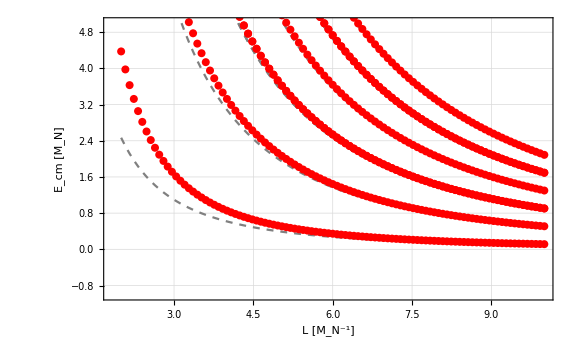

```mathematica
ListPlot[Join[(Transpose@{Llist,(Transpose@freelines)⟦#⟧})&/@Range[1,levelNum],(Transpose@{Llist,(Transpose@spectrum)⟦#⟧})&/@Range[1,levelNum]],Joined->Join[Table[True,{i,1,levelNum}],Table[False,{i,1,levelNum}]],PlotStyle->Join[Table[Directive[Gray,Dashed],{i,1,levelNum}],Table[Directive[Red,PointSize[0.01]],{i,1,levelNum}]],Frame->True,GridLines->Automatic,AxesLabel->{"L [M_N^-1]","E_cm [M_N]"},ImageSize->Large,PlotRange->{-1,5}]
```

```mathematica
prec=16;pcut=20;prnt=0;irreps="A1+";levelNum=8;g=10;
freelines={};spectrum={};
Llist=Range[2,10,8/100];
For[j=1,j≤Length@Llist,j++,L=Llist⟦j⟧;
levels0=EnergyLevelsProjection0[1,pcut,irreps];
(*Print["-----------------------------------"];*)
fakes=EnergyLevelsProjectionFree[1,pcut,irreps];
(*Print["-----------------------------------"];*)
levels=DeleteFakePole[levels0,fakes];
fakesTruncated=Table[fakes⟦i⟧,{i,1,levelNum}];
levelsTruncated=Table[levels⟦i⟧,{i,1,levelNum}];
AppendTo[freelines,fakesTruncated];
AppendTo[spectrum,levelsTruncated];
Print[j,"): L = ",N@L];
]
```

1): L = 2.

2): L = 2.08

3): L = 2.16

4): L = 2.24

5): L = 2.32

6): L = 2.4

7): L = 2.48

8): L = 2.56

9): L = 2.64

10): L = 2.72

11): L = 2.8

12): L = 2.88

13): L = 2.96

14): L = 3.04

15): L = 3.12

16): L = 3.2

17): L = 3.28

18): L = 3.36

19): L = 3.44

20): L = 3.52

21): L = 3.6

22): L = 3.68

23): L = 3.76

24): L = 3.84

25): L = 3.92

26): L = 4.

27): L = 4.08

28): L = 4.16

29): L = 4.24

30): L = 4.32

31): L = 4.4

32): L = 4.48

33): L = 4.56

34): L = 4.64

35): L = 4.72

36): L = 4.8

37): L = 4.88

38): L = 4.96

39): L = 5.04

40): L = 5.12

41): L = 5.2

42): L = 5.28

43): L = 5.36

44): L = 5.44

45): L = 5.52

46): L = 5.6

47): L = 5.68

48): L = 5.76

49): L = 5.84

50): L = 5.92

51): L = 6.

52): L = 6.08

53): L = 6.16

54): L = 6.24

55): L = 6.32

56): L = 6.4

57): L = 6.48

58): L = 6.56

59): L = 6.64

60): L = 6.72

61): L = 6.8

62): L = 6.88

63): L = 6.96

64): L = 7.04

65): L = 7.12

66): L = 7.2

67): L = 7.28

68): L = 7.36

69): L = 7.44

70): L = 7.52

71): L = 7.6

72): L = 7.68

73): L = 7.76

74): L = 7.84

75): L = 7.92

76): L = 8.

77): L = 8.08

78): L = 8.16

79): L = 8.24

80): L = 8.32

81): L = 8.4

82): L = 8.48

83): L = 8.56

84): L = 8.64

85): L = 8.72

86): L = 8.8

87): L = 8.88

88): L = 8.96

89): L = 9.04

90): L = 9.12

91): L = 9.2

92): L = 9.28

93): L = 9.36

94): L = 9.44

95): L = 9.52

96): L = 9.6

97): L = 9.68

98): L = 9.76

99): L = 9.84

100): L = 9.92

101): L = 10.

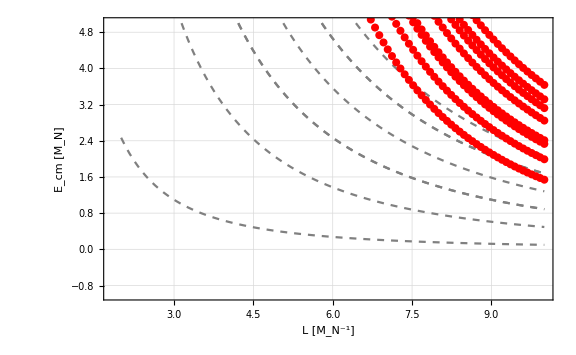

```mathematica
ListPlot[Join[(Transpose@{Llist,(Transpose@freelines)⟦#⟧})&/@Range[1,levelNum],(Transpose@{Llist,(Transpose@spectrum)⟦#⟧})&/@Range[1,levelNum]],Joined->Join[Table[True,{i,1,levelNum}],Table[False,{i,1,levelNum}]],PlotStyle->Join[Table[Directive[Gray,Dashed],{i,1,levelNum}],Table[Directive[Red,PointSize[0.01]],{i,1,levelNum}]],Frame->True,GridLines->Automatic,FrameLabel->{"L [M_N^-1]","E_cm [M_N]"},ImageSize->Large,PlotRange->{-1,5}]
```

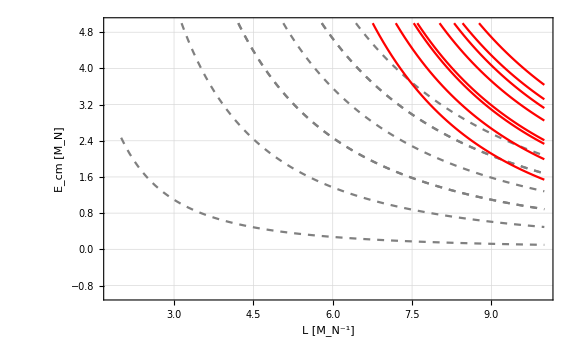

```mathematica
ListPlot[Join[(Transpose@{Llist,(Transpose@freelines)⟦#⟧})&/@Range[1,levelNum],(Transpose@{Llist,(Transpose@spectrum)⟦#⟧})&/@Range[1,levelNum]],Joined->Join[Table[True,{i,1,levelNum}],Table[True,{i,1,levelNum}]],PlotStyle->Join[Table[Directive[Gray,Dashed],{i,1,levelNum}],Table[Directive[Red],{i,1,levelNum}]],Frame->True,GridLines->Automatic,FrameLabel->{"L [M_N^-1]","E_cm [M_N]"},ImageSize->Large,PlotRange->{-1,5}]
```

```mathematica
prec=16;pcut=20;prnt=0;irreps="A1+";levelNum=8;g=3;
freelines={};spectrum={};
Llist=Range[2,10,8/100];
For[j=1,j≤Length@Llist,j++,L=Llist⟦j⟧;
levels0=EnergyLevelsProjection0[1,pcut,irreps];
(*Print["-----------------------------------"];*)
fakes=EnergyLevelsProjectionFree[1,pcut,irreps];
(*Print["-----------------------------------"];*)
levels=DeleteFakePole[levels0,fakes];
fakesTruncated=Table[fakes⟦i⟧,{i,1,levelNum}];
levelsTruncated=Table[levels⟦i⟧,{i,1,levelNum}];
AppendTo[freelines,fakesTruncated];
AppendTo[spectrum,levelsTruncated];
Print[j,"): L = ",N@L];
]
```

1): L = 2.

2): L = 2.08

3): L = 2.16

4): L = 2.24

5): L = 2.32

6): L = 2.4

7): L = 2.48

8): L = 2.56

9): L = 2.64

10): L = 2.72

11): L = 2.8

12): L = 2.88

13): L = 2.96

14): L = 3.04

15): L = 3.12

16): L = 3.2

17): L = 3.28

18): L = 3.36

19): L = 3.44

20): L = 3.52

21): L = 3.6

22): L = 3.68

23): L = 3.76

24): L = 3.84

25): L = 3.92

26): L = 4.

27): L = 4.08

28): L = 4.16

29): L = 4.24

30): L = 4.32

31): L = 4.4

32): L = 4.48

33): L = 4.56

34): L = 4.64

35): L = 4.72

36): L = 4.8

37): L = 4.88

38): L = 4.96

39): L = 5.04

40): L = 5.12

41): L = 5.2

42): L = 5.28

43): L = 5.36

44): L = 5.44

45): L = 5.52

46): L = 5.6

47): L = 5.68

48): L = 5.76

49): L = 5.84

50): L = 5.92

51): L = 6.

52): L = 6.08

53): L = 6.16

54): L = 6.24

55): L = 6.32

56): L = 6.4

57): L = 6.48

58): L = 6.56

59): L = 6.64

60): L = 6.72

61): L = 6.8

62): L = 6.88

63): L = 6.96

64): L = 7.04

65): L = 7.12

66): L = 7.2

67): L = 7.28

68): L = 7.36

69): L = 7.44

70): L = 7.52

71): L = 7.6

72): L = 7.68

73): L = 7.76

74): L = 7.84

75): L = 7.92

76): L = 8.

77): L = 8.08

78): L = 8.16

79): L = 8.24

80): L = 8.32

81): L = 8.4

82): L = 8.48

83): L = 8.56

84): L = 8.64

85): L = 8.72

86): L = 8.8

87): L = 8.88

88): L = 8.96

89): L = 9.04

90): L = 9.12

91): L = 9.2

92): L = 9.28

93): L = 9.36

94): L = 9.44

95): L = 9.52

96): L = 9.6

97): L = 9.68

98): L = 9.76

99): L = 9.84

100): L = 9.92

101): L = 10.

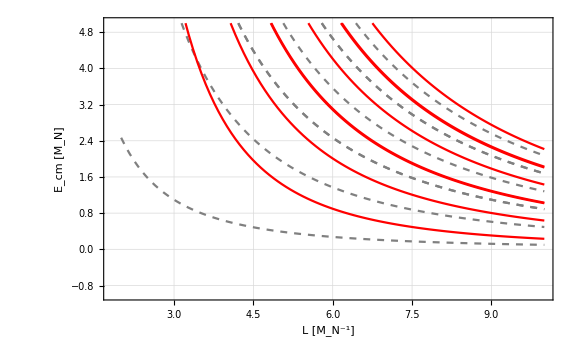

```mathematica
ListPlot[Join[(Transpose@{Llist,(Transpose@freelines)⟦#⟧})&/@Range[1,levelNum],(Transpose@{Llist,(Transpose@spectrum)⟦#⟧})&/@Range[1,levelNum]],Joined->Join[Table[True,{i,1,levelNum}],Table[True,{i,1,levelNum}]],PlotStyle->Join[Table[Directive[Gray,Dashed],{i,1,levelNum}],Table[Directive[Red],{i,1,levelNum}]],Frame->True,GridLines->Automatic,FrameLabel->{"L [M_N^-1]","E_cm [M_N]"},ImageSize->Large,PlotRange->{-1,5}]
```

```mathematica
cubicMOV⟦1,#⟧&/@{5,6,7}
cubicMOV⟦2,#⟧&/@{5,6,7}
cubicMOV⟦3,#⟧&/@{5,6,7}
cubicMOV⟦4,#⟧&/@{5,6,7}
cubicMOV⟦5,#⟧&/@{5,6,7}
cubicMOV⟦6,#⟧&/@{5,6,7}
```

{0,0,0}

{-1,0,0}

{0,0,-1}

{-1,-1,0}

{-1,0,-1}

{-1,-1,-1}

```mathematica
i=1;(cubicMOV⟦i,#⟧&/@{5,6,7}-{0,0,1/2}).(cubicMOV⟦i,#⟧&/@{5,6,7}-{0,0,1/2})
i=2;(cubicMOV⟦i,#⟧&/@{5,6,7}-{0,0,1/2}).(cubicMOV⟦i,#⟧&/@{5,6,7}-{0,0,1/2})
i=3;(cubicMOV⟦i,#⟧&/@{5,6,7}-{0,0,1/2}).(cubicMOV⟦i,#⟧&/@{5,6,7}-{0,0,1/2})
i=4;(cubicMOV⟦i,#⟧&/@{5,6,7}-{0,0,1/2}).(cubicMOV⟦i,#⟧&/@{5,6,7}-{0,0,1/2})
i=5;(cubicMOV⟦i,#⟧&/@{5,6,7}-{0,0,1/2}).(cubicMOV⟦i,#⟧&/@{5,6,7}-{0,0,1/2})
i=6;(cubicMOV⟦i,#⟧&/@{5,6,7}-{0,0,1/2}).(cubicMOV⟦i,#⟧&/@{5,6,7}-{0,0,1/2})
i=7;(cubicMOV⟦i,#⟧&/@{5,6,7}-{0,0,1/2}).(cubicMOV⟦i,#⟧&/@{5,6,7}-{0,0,1/2})
```

1/4

5/4

9/4

9/4

13/4

17/4

17/4

### V_SF and m_N=m'_N

```mathematica
V[p_,q_]:=VSF[p,q];mNp=mN;
```

#### A_1^+

```mathematica
prec=16;pcut=30;prnt=0;irreps="A1+";levelNum=8;
L=2π;
freeNum=ShellAnalysis[1,pcut,irreps,levelNum];
```

1): {0,0,0} --> A1+ x 1. ω = 0.25

2): {-1,0,0} --> A1+ x 1. ω = 1.25

3): {0,0,-1} --> A1+ x 1. ω = 2.25

4): {-1,-1,0} --> A1+ x 1. ω = 2.25

5): {-1,0,-1} --> A1+ x 1. ω = 3.25

6): {-1,-1,-1} --> A1+ x 1. ω = 4.25

7): {-2,0,0} --> A1+ x 1. ω = 4.25

8): {0,0,-2} --> A1+ x 1. ω = 6.25

9): {-2,-1,0} --> A1+ x 1. ω = 5.25

```mathematica
prec=16;pcut=20;prnt=0;irreps="A1+";levelNum=8;
freelines={};spectrum={};
Llist=Range[2,10,8/100];
For[j=1,j≤Length@Llist,j++,L=Llist⟦j⟧;
levels0=EnergyLevelsProjection0[1,pcut,irreps];
(*Print["-----------------------------------"];*)
fakes=EnergyLevelsProjectionFree[1,pcut,irreps];
(*Print["-----------------------------------"];*)
levels=DeleteFakePole[levels0,fakes];
fakesTruncated=Table[fakes⟦i⟧,{i,1,levelNum}];
levelsTruncated=Table[levels⟦i⟧,{i,1,levelNum}];
AppendTo[freelines,fakesTruncated];
AppendTo[spectrum,levelsTruncated];
Print[j,"): L = ",N@L];
]
```

1): L = 2.

2): L = 2.08

3): L = 2.16

4): L = 2.24

5): L = 2.32

6): L = 2.4

7): L = 2.48

8): L = 2.56

9): L = 2.64

10): L = 2.72

11): L = 2.8

12): L = 2.88

13): L = 2.96

14): L = 3.04

15): L = 3.12

16): L = 3.2

17): L = 3.28

18): L = 3.36

19): L = 3.44

20): L = 3.52

21): L = 3.6

22): L = 3.68

23): L = 3.76

24): L = 3.84

25): L = 3.92

26): L = 4.

27): L = 4.08

28): L = 4.16

29): L = 4.24

30): L = 4.32

31): L = 4.4

32): L = 4.48

33): L = 4.56

34): L = 4.64

35): L = 4.72

36): L = 4.8

37): L = 4.88

38): L = 4.96

39): L = 5.04

40): L = 5.12

41): L = 5.2

42): L = 5.28

43): L = 5.36

44): L = 5.44

45): L = 5.52

46): L = 5.6

47): L = 5.68

48): L = 5.76

49): L = 5.84

50): L = 5.92

51): L = 6.

52): L = 6.08

53): L = 6.16

54): L = 6.24

55): L = 6.32

56): L = 6.4

57): L = 6.48

58): L = 6.56

59): L = 6.64

60): L = 6.72

61): L = 6.8

62): L = 6.88

63): L = 6.96

64): L = 7.04

65): L = 7.12

66): L = 7.2

67): L = 7.28

68): L = 7.36

69): L = 7.44

70): L = 7.52

71): L = 7.6

72): L = 7.68

73): L = 7.76

74): L = 7.84

75): L = 7.92

76): L = 8.

77): L = 8.08

78): L = 8.16

79): L = 8.24

80): L = 8.32

81): L = 8.4

82): L = 8.48

83): L = 8.56

84): L = 8.64

85): L = 8.72

86): L = 8.8

87): L = 8.88

88): L = 8.96

89): L = 9.04

90): L = 9.12

91): L = 9.2

92): L = 9.28

93): L = 9.36

94): L = 9.44

95): L = 9.52

96): L = 9.6

97): L = 9.68

98): L = 9.76

99): L = 9.84

100): L = 9.92

101): L = 10.

```mathematica
dataFree=Transpose@Join[{N@Llist},Transpose@freelines];
dataSpectrum=Transpose@Join[{N@Llist},Transpose@spectrum];
Export["freelines_A1+.txt",dataFree,"Table","FieldSeparators"->" "];
Export["spectra_A1+.txt",dataSpectrum,"Table","FieldSeparators"->" "];
```

```mathematica
dataFree0=Import["freelines_A1+.txt","Table","FieldSeparators"->" "];
dataSpectrum0=Import["spectra_A1+.txt","Table","FieldSeparators"->" "];
plotFree=(Transpose@{(Transpose@dataFree0)⟦1⟧,(Transpose@dataFree0)⟦#⟧})&/@Range[2,levelNum+1];
plotSpectrum=(Transpose@{(Transpose@dataSpectrum0)⟦1⟧,(Transpose@dataSpectrum0)⟦#⟧})&/@Range[2,levelNum+1];
```

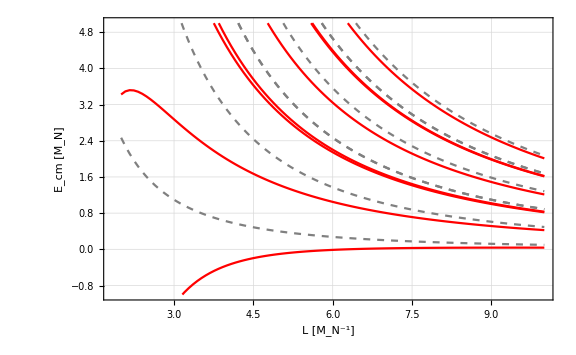

```mathematica
plotsave=ListPlot[Join[plotFree,plotSpectrum],Joined->Join[Table[True,{i,1,levelNum}],Table[True,{i,1,levelNum}]],PlotStyle->Join[Table[Directive[Gray,Dashed],{i,1,levelNum}],Table[Directive[Red],{i,1,levelNum}]],Frame->True,GridLines->Automatic,FrameLabel->{"L [M_N^-1]","E_cm [M_N]"},ImageSize->Large,PlotRange->{-1,5}]
```

```mathematica
Export["spectrum_A1+.pdf",plotsave];
```

#### E^+

```mathematica
prec=16;pcut=30;prnt=0;irreps="E+";levelNum=8;
L=2π;
freeNum=ShellAnalysis[1,pcut,irreps,levelNum];
```

5): {-1,0,-1} --> E+ x 1. ω = 3.25

6): {-1,-1,-1} --> E+ x 1. ω = 4.25

10): {-2,0,-1} --> E+ x 1. ω = 6.25

11): {-1,0,-2} --> E+ x 1. ω = 7.25

12): {-2,-1,-1} --> E+ x 2. ω = 7.25

13): {-1,-1,-2} --> E+ x 1. ω = 8.25

15): {-2,0,-2} --> E+ x 1. ω = 10.25

18): {-2,-2,-1} --> E+ x 1. ω = 10.25

```mathematica
prec=16;pcut=30;prnt=0;irreps="E+";levelNum=8;
freelines={};spectrum={};
Llist=Range[2,10,8/100];
For[j=1,j≤Length@Llist,j++,L=Llist⟦j⟧;
levels0=EnergyLevelsProjection0[1,pcut,irreps];
(*Print["-----------------------------------"];*)
fakes=EnergyLevelsProjectionFree[1,pcut,irreps];
(*Print["-----------------------------------"];*)
levels=DeleteFakePole[levels0,fakes];
fakesTruncated=Table[fakes⟦i⟧,{i,1,levelNum}];
levelsTruncated=Table[levels⟦i⟧,{i,1,levelNum}];
AppendTo[freelines,fakesTruncated];
AppendTo[spectrum,levelsTruncated];
Print[j,"): L = ",N@L];
]
```

1): L = 2.

2): L = 2.08

3): L = 2.16

4): L = 2.24

5): L = 2.32

6): L = 2.4

7): L = 2.48

8): L = 2.56

9): L = 2.64

10): L = 2.72

11): L = 2.8

12): L = 2.88

13): L = 2.96

14): L = 3.04

15): L = 3.12

16): L = 3.2

17): L = 3.28

18): L = 3.36

19): L = 3.44

20): L = 3.52

21): L = 3.6

22): L = 3.68

23): L = 3.76

24): L = 3.84

25): L = 3.92

26): L = 4.

27): L = 4.08

28): L = 4.16

29): L = 4.24

30): L = 4.32

31): L = 4.4

32): L = 4.48

33): L = 4.56

34): L = 4.64

35): L = 4.72

36): L = 4.8

37): L = 4.88

38): L = 4.96

39): L = 5.04

40): L = 5.12

41): L = 5.2

42): L = 5.28

43): L = 5.36

44): L = 5.44

45): L = 5.52

46): L = 5.6

47): L = 5.68

48): L = 5.76

49): L = 5.84

50): L = 5.92

51): L = 6.

52): L = 6.08

53): L = 6.16

54): L = 6.24

55): L = 6.32

56): L = 6.4

57): L = 6.48

58): L = 6.56

59): L = 6.64

60): L = 6.72

61): L = 6.8

62): L = 6.88

63): L = 6.96

64): L = 7.04

65): L = 7.12

66): L = 7.2

67): L = 7.28

68): L = 7.36

69): L = 7.44

70): L = 7.52

71): L = 7.6

72): L = 7.68

73): L = 7.76

74): L = 7.84

75): L = 7.92

76): L = 8.

77): L = 8.08

78): L = 8.16

79): L = 8.24

80): L = 8.32

81): L = 8.4

82): L = 8.48

83): L = 8.56

84): L = 8.64

85): L = 8.72

86): L = 8.8

87): L = 8.88

88): L = 8.96

89): L = 9.04

90): L = 9.12

91): L = 9.2

92): L = 9.28

93): L = 9.36

94): L = 9.44

95): L = 9.52

96): L = 9.6

97): L = 9.68

98): L = 9.76

99): L = 9.84

100): L = 9.92

101): L = 10.

```mathematica
prec=16;pcut=30;prnt=0;irreps="E+";levelNum=8;
freelines={};
Llist=Range[2,10,8/100];
For[j=1,j≤Length@Llist,j++,L=Llist⟦j⟧;
(*Print["-----------------------------------"];*)
fakes=EnergyLevelsProjectionFree[1,pcut,irreps];
(*Print["-----------------------------------"];*)
equalPrecision[x1_,x2_]:=(Abs@(x1-x2)≤10^-9);
fakes=DeleteDuplicates[fakes,equalPrecision];
fakesTruncated=Table[fakes⟦i⟧,{i,1,freeNum}];

AppendTo[freelines,fakesTruncated];

Print[j,"): L = ",N@L];
]
```

1): L = 2.

2): L = 2.08

3): L = 2.16

4): L = 2.24

5): L = 2.32

6): L = 2.4

7): L = 2.48

8): L = 2.56

9): L = 2.64

10): L = 2.72

11): L = 2.8

12): L = 2.88

13): L = 2.96

14): L = 3.04

15): L = 3.12

16): L = 3.2

17): L = 3.28

18): L = 3.36

19): L = 3.44

20): L = 3.52

21): L = 3.6

22): L = 3.68

23): L = 3.76

24): L = 3.84

25): L = 3.92

26): L = 4.

27): L = 4.08

28): L = 4.16

29): L = 4.24

30): L = 4.32

31): L = 4.4

32): L = 4.48

33): L = 4.56

34): L = 4.64

35): L = 4.72

36): L = 4.8

37): L = 4.88

38): L = 4.96

39): L = 5.04

40): L = 5.12

41): L = 5.2

42): L = 5.28

43): L = 5.36

44): L = 5.44

45): L = 5.52

46): L = 5.6

47): L = 5.68

48): L = 5.76

49): L = 5.84

50): L = 5.92

51): L = 6.

52): L = 6.08

53): L = 6.16

54): L = 6.24

55): L = 6.32

56): L = 6.4

57): L = 6.48

58): L = 6.56

59): L = 6.64

60): L = 6.72

61): L = 6.8

62): L = 6.88

63): L = 6.96

64): L = 7.04

65): L = 7.12

66): L = 7.2

67): L = 7.28

68): L = 7.36

69): L = 7.44

70): L = 7.52

71): L = 7.6

72): L = 7.68

73): L = 7.76

74): L = 7.84

75): L = 7.92

76): L = 8.

77): L = 8.08

78): L = 8.16

79): L = 8.24

80): L = 8.32

81): L = 8.4

82): L = 8.48

83): L = 8.56

84): L = 8.64

85): L = 8.72

86): L = 8.8

87): L = 8.88

88): L = 8.96

89): L = 9.04

90): L = 9.12

91): L = 9.2

92): L = 9.28

93): L = 9.36

94): L = 9.44

95): L = 9.52

96): L = 9.6

97): L = 9.68

98): L = 9.76

99): L = 9.84

100): L = 9.92

101): L = 10.

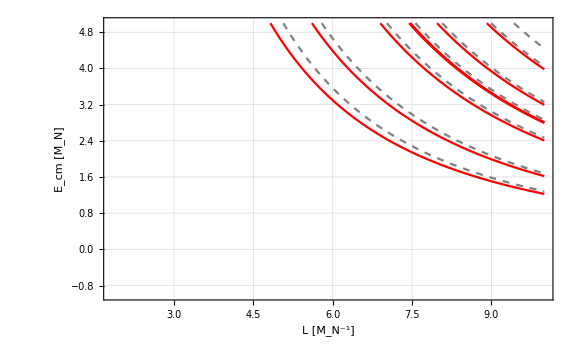

```mathematica
ListPlot[Join[(Transpose@{Llist,(Transpose@spectrum)⟦#⟧})&/@Range[1,levelNum],(Transpose@{Llist,(Transpose@freelines)⟦#⟧})&/@Range[1,freeNum]],Joined->Join[Table[True,{i,1,levelNum}],Table[True,{i,1,freeNum}]],PlotStyle->Join[Table[Directive[Red],{i,1,levelNum}],Table[Directive[Gray,Dashed],{i,1,freeNum}]],Frame->True,GridLines->Automatic,FrameLabel->{"L [M_N^-1]","E_cm [M_N]"},ImageSize->Large,PlotRange->{-1,5}]
```

#### B_2^-

```mathematica
prec=16;pcut=30;prnt=0;irreps="B2-";levelNum=8;
L=2π;
freeNum=ShellAnalysis[1,pcut,irreps,levelNum];
```

6): {-1,-1,-1} --> B2- x 1. ω = 4.25

12): {-2,-1,-1} --> B2- x 1. ω = 7.25

13): {-1,-1,-2} --> B2- x 1. ω = 8.25

18): {-2,-2,-1} --> B2- x 1. ω = 10.25

19): {-2,-1,-2} --> B2- x 1. ω = 11.25

23): {-3,-1,-1} --> B2- x 1. ω = 12.25

24): {-1,-1,-3} --> B2- x 1. ω = 14.25

25): {-2,-2,-2} --> B2- x 1. ω = 14.25

29): {-3,-2,-1} --> B2- x 1. ω = 15.25

```mathematica
prec=16;pcut=30;prnt=0;irreps="B2-";levelNum=8;
freelines={};spectrum={};
Llist=Range[2,10,8/100];
For[j=1,j≤Length@Llist,j++,L=Llist⟦j⟧;
levels0=EnergyLevelsProjection0[1,pcut,irreps];
(*Print["-----------------------------------"];*)
fakes=EnergyLevelsProjectionFree[1,pcut,irreps];
(*Print["-----------------------------------"];*)
levels=DeleteFakePole[levels0,fakes];
fakesTruncated=Table[fakes⟦i⟧,{i,1,levelNum}];
levelsTruncated=Table[levels⟦i⟧,{i,1,levelNum}];
AppendTo[freelines,fakesTruncated];
AppendTo[spectrum,levelsTruncated];
Print[j,"): L = ",N@L];
]
```

1): L = 2.

2): L = 2.08

3): L = 2.16

4): L = 2.24

5): L = 2.32

6): L = 2.4

7): L = 2.48

8): L = 2.56

9): L = 2.64

10): L = 2.72

11): L = 2.8

12): L = 2.88

13): L = 2.96

14): L = 3.04

15): L = 3.12

16): L = 3.2

17): L = 3.28

18): L = 3.36

19): L = 3.44

20): L = 3.52

21): L = 3.6

22): L = 3.68

23): L = 3.76

24): L = 3.84

25): L = 3.92

26): L = 4.

27): L = 4.08

28): L = 4.16

29): L = 4.24

30): L = 4.32

31): L = 4.4

32): L = 4.48

33): L = 4.56

34): L = 4.64

35): L = 4.72

36): L = 4.8

37): L = 4.88

38): L = 4.96

39): L = 5.04

40): L = 5.12

41): L = 5.2

42): L = 5.28

43): L = 5.36

44): L = 5.44

45): L = 5.52

46): L = 5.6

47): L = 5.68

48): L = 5.76

49): L = 5.84

50): L = 5.92

51): L = 6.

52): L = 6.08

53): L = 6.16

54): L = 6.24

55): L = 6.32

56): L = 6.4

57): L = 6.48

58): L = 6.56

59): L = 6.64

60): L = 6.72

61): L = 6.8

62): L = 6.88

63): L = 6.96

64): L = 7.04

65): L = 7.12

66): L = 7.2

67): L = 7.28

68): L = 7.36

69): L = 7.44

70): L = 7.52

71): L = 7.6

72): L = 7.68

73): L = 7.76

74): L = 7.84

75): L = 7.92

76): L = 8.

77): L = 8.08

78): L = 8.16

79): L = 8.24

80): L = 8.32

81): L = 8.4

82): L = 8.48

83): L = 8.56

84): L = 8.64

85): L = 8.72

86): L = 8.8

87): L = 8.88

88): L = 8.96

89): L = 9.04

90): L = 9.12

91): L = 9.2

92): L = 9.28

93): L = 9.36

94): L = 9.44

95): L = 9.52

96): L = 9.6

97): L = 9.68

98): L = 9.76

99): L = 9.84

100): L = 9.92

101): L = 10.

```mathematica
prec=16;pcut=30;prnt=0;irreps="B2-";levelNum=8;
freelines={};
Llist=Range[2,10,8/100];
For[j=1,j≤Length@Llist,j++,L=Llist⟦j⟧;
(*Print["-----------------------------------"];*)
fakes=EnergyLevelsProjectionFree[1,pcut,irreps];
(*Print["-----------------------------------"];*)
equalPrecision[x1_,x2_]:=(Abs@(x1-x2)≤10^-9);
fakes=DeleteDuplicates[fakes,equalPrecision];
fakesTruncated=Table[fakes⟦i⟧,{i,1,freeNum}];

AppendTo[freelines,fakesTruncated];

Print[j,"): L = ",N@L];
]
```

1): L = 2.

2): L = 2.08

3): L = 2.16

4): L = 2.24

5): L = 2.32

6): L = 2.4

7): L = 2.48

8): L = 2.56

9): L = 2.64

10): L = 2.72

11): L = 2.8

12): L = 2.88

13): L = 2.96

14): L = 3.04

15): L = 3.12

16): L = 3.2

17): L = 3.28

18): L = 3.36

19): L = 3.44

20): L = 3.52

21): L = 3.6

22): L = 3.68

23): L = 3.76

24): L = 3.84

25): L = 3.92

26): L = 4.

27): L = 4.08

28): L = 4.16

29): L = 4.24

30): L = 4.32

31): L = 4.4

32): L = 4.48

33): L = 4.56

34): L = 4.64

35): L = 4.72

36): L = 4.8

37): L = 4.88

38): L = 4.96

39): L = 5.04

40): L = 5.12

41): L = 5.2

42): L = 5.28

43): L = 5.36

44): L = 5.44

45): L = 5.52

46): L = 5.6

47): L = 5.68

48): L = 5.76

49): L = 5.84

50): L = 5.92

51): L = 6.

52): L = 6.08

53): L = 6.16

54): L = 6.24

55): L = 6.32

56): L = 6.4

57): L = 6.48

58): L = 6.56

59): L = 6.64

60): L = 6.72

61): L = 6.8

62): L = 6.88

63): L = 6.96

64): L = 7.04

65): L = 7.12

66): L = 7.2

67): L = 7.28

68): L = 7.36

69): L = 7.44

70): L = 7.52

71): L = 7.6

72): L = 7.68

73): L = 7.76

74): L = 7.84

75): L = 7.92

76): L = 8.

77): L = 8.08

78): L = 8.16

79): L = 8.24

80): L = 8.32

81): L = 8.4

82): L = 8.48

83): L = 8.56

84): L = 8.64

85): L = 8.72

86): L = 8.8

87): L = 8.88

88): L = 8.96

89): L = 9.04

90): L = 9.12

91): L = 9.2

92): L = 9.28

93): L = 9.36

94): L = 9.44

95): L = 9.52

96): L = 9.6

97): L = 9.68

98): L = 9.76

99): L = 9.84

100): L = 9.92

101): L = 10.

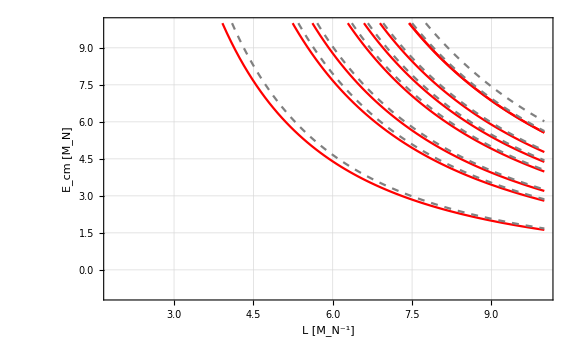

```mathematica
ListPlot[Join[(Transpose@{Llist,(Transpose@spectrum)⟦#⟧})&/@Range[1,levelNum],(Transpose@{Llist,(Transpose@freelines)⟦#⟧})&/@Range[1,freeNum]],Joined->Join[Table[True,{i,1,levelNum}],Table[True,{i,1,freeNum}]],PlotStyle->Join[Table[Directive[Red],{i,1,levelNum}],Table[Directive[Gray,Dashed],{i,1,freeNum}]],Frame->True,GridLines->Automatic,FrameLabel->{"L [M_N^-1]","E_cm [M_N]"},ImageSize->Large,PlotRange->{-1,10}]
```

### V_SF and m_N≠m'_N

```mathematica
V[p_,q_]:=VSF[p,q];mNp=3/2;
```

#### A_1^+

```mathematica
prec=16;pcut=30;prnt=0;irreps="A1+";levelNum=8;
L=2π;
freeNum=ShellAnalysis[1,pcut,irreps,levelNum];
```

1): {0,0,0} --> A1+ x 1. ω = 0.133333

2): {-1,0,0} --> A1+ x 1. ω = 0.966667

3): {0,0,-1} --> A1+ x 1. ω = 1.63333

4): {-1,-1,0} --> A1+ x 1. ω = 1.8

5): {-1,0,-1} --> A1+ x 1. ω = 2.46667

6): {-1,-1,-1} --> A1+ x 1. ω = 3.3

7): {-2,0,0} --> A1+ x 1. ω = 3.46667

8): {0,0,-2} --> A1+ x 1. ω = 4.8

9): {-2,-1,0} --> A1+ x 1. ω = 4.3

```mathematica
prec=16;pcut=20;prnt=0;irreps="A1+";levelNum=8;
freelines={};spectrum={};
Llist=Range[2,10,8/100];
For[j=1,j≤Length@Llist,j++,L=Llist⟦j⟧;
levels0=EnergyLevelsProjection0[1,pcut,irreps];
(*Print["-----------------------------------"];*)
fakes=EnergyLevelsProjectionFree[1,pcut,irreps];
(*Print["-----------------------------------"];*)
levels=DeleteFakePole[levels0,fakes];
fakesTruncated=Table[fakes⟦i⟧,{i,1,levelNum}];
levelsTruncated=Table[levels⟦i⟧,{i,1,levelNum}];
AppendTo[freelines,fakesTruncated];
AppendTo[spectrum,levelsTruncated];
Print[j,"): L = ",N@L];
]
```

1): L = 2.

2): L = 2.08

3): L = 2.16

4): L = 2.24

5): L = 2.32

6): L = 2.4

7): L = 2.48

8): L = 2.56

9): L = 2.64

10): L = 2.72

11): L = 2.8

12): L = 2.88

13): L = 2.96

14): L = 3.04

15): L = 3.12

16): L = 3.2

17): L = 3.28

18): L = 3.36

19): L = 3.44

20): L = 3.52

21): L = 3.6

22): L = 3.68

23): L = 3.76

24): L = 3.84

25): L = 3.92

26): L = 4.

27): L = 4.08

28): L = 4.16

29): L = 4.24

30): L = 4.32

31): L = 4.4

32): L = 4.48

33): L = 4.56

34): L = 4.64

35): L = 4.72

36): L = 4.8

37): L = 4.88

38): L = 4.96

39): L = 5.04

40): L = 5.12

41): L = 5.2

42): L = 5.28

43): L = 5.36

44): L = 5.44

45): L = 5.52

46): L = 5.6

47): L = 5.68

48): L = 5.76

49): L = 5.84

50): L = 5.92

51): L = 6.

52): L = 6.08

53): L = 6.16

54): L = 6.24

55): L = 6.32

56): L = 6.4

57): L = 6.48

58): L = 6.56

59): L = 6.64

60): L = 6.72

61): L = 6.8

62): L = 6.88

63): L = 6.96

64): L = 7.04

65): L = 7.12

66): L = 7.2

67): L = 7.28

68): L = 7.36

69): L = 7.44

70): L = 7.52

71): L = 7.6

72): L = 7.68

73): L = 7.76

74): L = 7.84

75): L = 7.92

76): L = 8.

77): L = 8.08

78): L = 8.16

79): L = 8.24

80): L = 8.32

81): L = 8.4

82): L = 8.48

83): L = 8.56

84): L = 8.64

85): L = 8.72

86): L = 8.8

87): L = 8.88

88): L = 8.96

89): L = 9.04

90): L = 9.12

91): L = 9.2

92): L = 9.28

93): L = 9.36

94): L = 9.44

95): L = 9.52

96): L = 9.6

97): L = 9.68

98): L = 9.76

99): L = 9.84

100): L = 9.92

101): L = 10.

```mathematica
dataFree=Transpose@Join[{N@Llist},Transpose@freelines];
dataSpectrum=Transpose@Join[{N@Llist},Transpose@spectrum];
Export["freelines_A1+_2.txt",dataFree,"Table","FieldSeparators"->" "];
Export["spectra_A1+_2.txt",dataSpectrum,"Table","FieldSeparators"->" "];
```

```mathematica
dataFree0=Import["freelines_A1+_2.txt","Table","FieldSeparators"->" "];
dataSpectrum0=Import["spectra_A1+_2.txt","Table","FieldSeparators"->" "];
plotFree=(Transpose@{(Transpose@dataFree0)⟦1⟧,(Transpose@dataFree0)⟦#⟧})&/@Range[2,levelNum+1];
plotSpectrum=(Transpose@{(Transpose@dataSpectrum0)⟦1⟧,(Transpose@dataSpectrum0)⟦#⟧})&/@Range[2,levelNum+1];
```

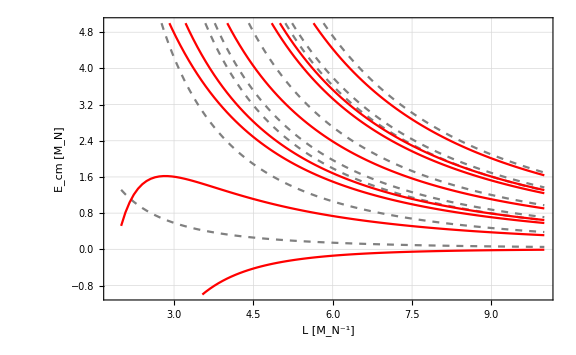

```mathematica
plotsave=ListPlot[Join[plotFree,plotSpectrum],Joined->Join[Table[True,{i,1,levelNum}],Table[True,{i,1,levelNum}]],PlotStyle->Join[Table[Directive[Gray,Dashed],{i,1,levelNum}],Table[Directive[Red],{i,1,levelNum}]],Frame->True,GridLines->Automatic,FrameLabel->{"L [M_N^-1]","E_cm [M_N]"},ImageSize->Large,PlotRange->{-1,5}]
```

```mathematica
Export["spectrum_A1+_2.pdf",plotsave];
```

#### E^+

```mathematica
prec=16;pcut=30;prnt=0;irreps="E+";levelNum=8;
freelines={};spectrum={};
Llist=Range[2,10,8/100];
For[j=1,j≤Length@Llist,j++,L=Llist⟦j⟧;
levels0=EnergyLevelsProjection0[1,pcut,irreps];
(*Print["-----------------------------------"];*)
fakes=EnergyLevelsProjectionFree[1,pcut,irreps];
(*Print["-----------------------------------"];*)
levels=DeleteFakePole[levels0,fakes];
fakesTruncated=Table[fakes⟦i⟧,{i,1,levelNum}];
levelsTruncated=Table[levels⟦i⟧,{i,1,levelNum}];
AppendTo[freelines,fakesTruncated];
AppendTo[spectrum,levelsTruncated];
Print[j,"): L = ",N@L];
]
```

1): L = 2.

2): L = 2.08

3): L = 2.16

4): L = 2.24

5): L = 2.32

6): L = 2.4

7): L = 2.48

8): L = 2.56

9): L = 2.64

10): L = 2.72

11): L = 2.8

12): L = 2.88

13): L = 2.96

14): L = 3.04

15): L = 3.12

16): L = 3.2

17): L = 3.28

18): L = 3.36

19): L = 3.44

20): L = 3.52

21): L = 3.6

22): L = 3.68

23): L = 3.76

24): L = 3.84

25): L = 3.92

26): L = 4.

27): L = 4.08

28): L = 4.16

29): L = 4.24

30): L = 4.32

31): L = 4.4

32): L = 4.48

33): L = 4.56

34): L = 4.64

35): L = 4.72

36): L = 4.8

37): L = 4.88

38): L = 4.96

39): L = 5.04

40): L = 5.12

41): L = 5.2

42): L = 5.28

43): L = 5.36

44): L = 5.44

45): L = 5.52

46): L = 5.6

47): L = 5.68

48): L = 5.76

49): L = 5.84

50): L = 5.92

51): L = 6.

52): L = 6.08

53): L = 6.16

54): L = 6.24

55): L = 6.32

56): L = 6.4

57): L = 6.48

58): L = 6.56

59): L = 6.64

60): L = 6.72

61): L = 6.8

62): L = 6.88

63): L = 6.96

64): L = 7.04

65): L = 7.12

66): L = 7.2

67): L = 7.28

68): L = 7.36

69): L = 7.44

70): L = 7.52

71): L = 7.6

72): L = 7.68

73): L = 7.76

74): L = 7.84

75): L = 7.92

76): L = 8.

77): L = 8.08

78): L = 8.16

79): L = 8.24

80): L = 8.32

81): L = 8.4

82): L = 8.48

83): L = 8.56

84): L = 8.64

85): L = 8.72

86): L = 8.8

87): L = 8.88

88): L = 8.96

89): L = 9.04

90): L = 9.12

91): L = 9.2

92): L = 9.28

93): L = 9.36

94): L = 9.44

95): L = 9.52

96): L = 9.6

97): L = 9.68

98): L = 9.76

99): L = 9.84

100): L = 9.92

101): L = 10.

```mathematica
L=2π;
freeNum=ShellAnalysis[1,pcut,irreps,levelNum];
```

5): {-1,0,-1} --> E+ x 1. ω = 2.46667

6): {-1,-1,-1} --> E+ x 1. ω = 3.3

10): {-2,0,-1} --> E+ x 1. ω = 4.96667

11): {-1,0,-2} --> E+ x 1. ω = 5.63333

12): {-2,-1,-1} --> E+ x 2. ω = 5.8

13): {-1,-1,-2} --> E+ x 1. ω = 6.46667

15): {-2,0,-2} --> E+ x 1. ω = 8.13333

18): {-2,-2,-1} --> E+ x 1. ω = 8.3

```mathematica
prec=16;pcut=30;prnt=0;irreps="E+";levelNum=8;
freelines={};
Llist=Range[2,10,8/100];
For[j=1,j≤Length@Llist,j++,L=Llist⟦j⟧;
(*Print["-----------------------------------"];*)
fakes=EnergyLevelsProjectionFree[1,pcut,irreps];
(*Print["-----------------------------------"];*)
equalPrecision[x1_,x2_]:=(Abs@(x1-x2)≤10^-9);
fakes=DeleteDuplicates[fakes,equalPrecision];
fakesTruncated=Table[fakes⟦i⟧,{i,1,freeNum}];

AppendTo[freelines,fakesTruncated];

Print[j,"): L = ",N@L];
]
```

1): L = 2.

2): L = 2.08

3): L = 2.16

4): L = 2.24

5): L = 2.32

6): L = 2.4

7): L = 2.48

8): L = 2.56

9): L = 2.64

10): L = 2.72

11): L = 2.8

12): L = 2.88

13): L = 2.96

14): L = 3.04

15): L = 3.12

16): L = 3.2

17): L = 3.28

18): L = 3.36

19): L = 3.44

20): L = 3.52

21): L = 3.6

22): L = 3.68

23): L = 3.76

24): L = 3.84

25): L = 3.92

26): L = 4.

27): L = 4.08

28): L = 4.16

29): L = 4.24

30): L = 4.32

31): L = 4.4

32): L = 4.48

33): L = 4.56

34): L = 4.64

35): L = 4.72

36): L = 4.8

37): L = 4.88

38): L = 4.96

39): L = 5.04

40): L = 5.12

41): L = 5.2

42): L = 5.28

43): L = 5.36

44): L = 5.44

45): L = 5.52

46): L = 5.6

47): L = 5.68

48): L = 5.76

49): L = 5.84

50): L = 5.92

51): L = 6.

52): L = 6.08

53): L = 6.16

54): L = 6.24

55): L = 6.32

56): L = 6.4

57): L = 6.48

58): L = 6.56

59): L = 6.64

60): L = 6.72

61): L = 6.8

62): L = 6.88

63): L = 6.96

64): L = 7.04

65): L = 7.12

66): L = 7.2

67): L = 7.28

68): L = 7.36

69): L = 7.44

70): L = 7.52

71): L = 7.6

72): L = 7.68

73): L = 7.76

74): L = 7.84

75): L = 7.92

76): L = 8.

77): L = 8.08

78): L = 8.16

79): L = 8.24

80): L = 8.32

81): L = 8.4

82): L = 8.48

83): L = 8.56

84): L = 8.64

85): L = 8.72

86): L = 8.8

87): L = 8.88

88): L = 8.96

89): L = 9.04

90): L = 9.12

91): L = 9.2

92): L = 9.28

93): L = 9.36

94): L = 9.44

95): L = 9.52

96): L = 9.6

97): L = 9.68

98): L = 9.76

99): L = 9.84

100): L = 9.92

101): L = 10.

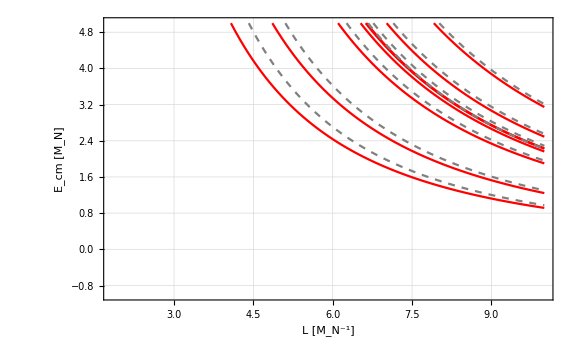

```mathematica
ListPlot[Join[(Transpose@{Llist,(Transpose@spectrum)⟦#⟧})&/@Range[1,levelNum],(Transpose@{Llist,(Transpose@freelines)⟦#⟧})&/@Range[1,freeNum]],Joined->Join[Table[True,{i,1,levelNum}],Table[True,{i,1,freeNum}]],PlotStyle->Join[Table[Directive[Red],{i,1,levelNum}],Table[Directive[Gray,Dashed],{i,1,freeNum}]],Frame->True,GridLines->Automatic,FrameLabel->{"L [M_N^-1]","E_cm [M_N]"},ImageSize->Large,PlotRange->{-1,5}]
```

#### B_2^-

```mathematica
prec=16;pcut=30;prnt=0;irreps="B2-";levelNum=8;
L=2π;
freeNum=ShellAnalysis[1,pcut,irreps,levelNum];
```

6): {-1,-1,-1} --> B2- x 1. ω = 3.3

12): {-2,-1,-1} --> B2- x 1. ω = 5.8

13): {-1,-1,-2} --> B2- x 1. ω = 6.46667

18): {-2,-2,-1} --> B2- x 1. ω = 8.3

19): {-2,-1,-2} --> B2- x 1. ω = 8.96667

23): {-3,-1,-1} --> B2- x 1. ω = 9.96667

24): {-1,-1,-3} --> B2- x 1. ω = 11.3

25): {-2,-2,-2} --> B2- x 1. ω = 11.4667

29): {-3,-2,-1} --> B2- x 1. ω = 12.4667

```mathematica
prec=16;pcut=30;prnt=0;irreps="B2-";levelNum=8;
freelines={};spectrum={};
Llist=Range[2,10,8/100];
For[j=1,j≤Length@Llist,j++,L=Llist⟦j⟧;
levels0=EnergyLevelsProjection0[1,pcut,irreps];
(*Print["-----------------------------------"];*)
fakes=EnergyLevelsProjectionFree[1,pcut,irreps];
(*Print["-----------------------------------"];*)
levels=DeleteFakePole[levels0,fakes];
fakesTruncated=Table[fakes⟦i⟧,{i,1,levelNum}];
levelsTruncated=Table[levels⟦i⟧,{i,1,levelNum}];
AppendTo[freelines,fakesTruncated];
AppendTo[spectrum,levelsTruncated];
Print[j,"): L = ",N@L];
]
```

1): L = 2.

2): L = 2.08

3): L = 2.16

4): L = 2.24

5): L = 2.32

6): L = 2.4

7): L = 2.48

8): L = 2.56

9): L = 2.64

10): L = 2.72

11): L = 2.8

12): L = 2.88

13): L = 2.96

14): L = 3.04

15): L = 3.12

16): L = 3.2

17): L = 3.28

18): L = 3.36

19): L = 3.44

20): L = 3.52

21): L = 3.6

22): L = 3.68

23): L = 3.76

24): L = 3.84

25): L = 3.92

26): L = 4.

27): L = 4.08

28): L = 4.16

29): L = 4.24

30): L = 4.32

31): L = 4.4

32): L = 4.48

33): L = 4.56

34): L = 4.64

35): L = 4.72

36): L = 4.8

37): L = 4.88

38): L = 4.96

39): L = 5.04

40): L = 5.12

41): L = 5.2

42): L = 5.28

43): L = 5.36

44): L = 5.44

45): L = 5.52

46): L = 5.6

47): L = 5.68

48): L = 5.76

49): L = 5.84

50): L = 5.92

51): L = 6.

52): L = 6.08

53): L = 6.16

54): L = 6.24

55): L = 6.32

56): L = 6.4

57): L = 6.48

58): L = 6.56

59): L = 6.64

60): L = 6.72

61): L = 6.8

62): L = 6.88

63): L = 6.96

64): L = 7.04

65): L = 7.12

66): L = 7.2

67): L = 7.28

68): L = 7.36

69): L = 7.44

70): L = 7.52

71): L = 7.6

72): L = 7.68

73): L = 7.76

74): L = 7.84

75): L = 7.92

76): L = 8.

77): L = 8.08

78): L = 8.16

79): L = 8.24

80): L = 8.32

81): L = 8.4

82): L = 8.48

83): L = 8.56

84): L = 8.64

85): L = 8.72

86): L = 8.8

87): L = 8.88

88): L = 8.96

89): L = 9.04

90): L = 9.12

91): L = 9.2

92): L = 9.28

93): L = 9.36

94): L = 9.44

95): L = 9.52

96): L = 9.6

97): L = 9.68

98): L = 9.76

99): L = 9.84

100): L = 9.92

101): L = 10.

```mathematica
prec=16;pcut=30;prnt=0;irreps="B2-";levelNum=8;
freelines={};
Llist=Range[2,10,8/100];
For[j=1,j≤Length@Llist,j++,L=Llist⟦j⟧;
(*Print["-----------------------------------"];*)
fakes=EnergyLevelsProjectionFree[1,pcut,irreps];
(*Print["-----------------------------------"];*)
equalPrecision[x1_,x2_]:=(Abs@(x1-x2)≤10^-9);
fakes=DeleteDuplicates[fakes,equalPrecision];
fakesTruncated=Table[fakes⟦i⟧,{i,1,freeNum}];

AppendTo[freelines,fakesTruncated];

Print[j,"): L = ",N@L];
]
```

1): L = 2.

2): L = 2.08

3): L = 2.16

4): L = 2.24

5): L = 2.32

6): L = 2.4

7): L = 2.48

8): L = 2.56

9): L = 2.64

10): L = 2.72

11): L = 2.8

12): L = 2.88

13): L = 2.96

14): L = 3.04

15): L = 3.12

16): L = 3.2

17): L = 3.28

18): L = 3.36

19): L = 3.44

20): L = 3.52

21): L = 3.6

22): L = 3.68

23): L = 3.76

24): L = 3.84

25): L = 3.92

26): L = 4.

27): L = 4.08

28): L = 4.16

29): L = 4.24

30): L = 4.32

31): L = 4.4

32): L = 4.48

33): L = 4.56

34): L = 4.64

35): L = 4.72

36): L = 4.8

37): L = 4.88

38): L = 4.96

39): L = 5.04

40): L = 5.12

41): L = 5.2

42): L = 5.28

43): L = 5.36

44): L = 5.44

45): L = 5.52

46): L = 5.6

47): L = 5.68

48): L = 5.76

49): L = 5.84

50): L = 5.92

51): L = 6.

52): L = 6.08

53): L = 6.16

54): L = 6.24

55): L = 6.32

56): L = 6.4

57): L = 6.48

58): L = 6.56

59): L = 6.64

60): L = 6.72

61): L = 6.8

62): L = 6.88

63): L = 6.96

64): L = 7.04

65): L = 7.12

66): L = 7.2

67): L = 7.28

68): L = 7.36

69): L = 7.44

70): L = 7.52

71): L = 7.6

72): L = 7.68

73): L = 7.76

74): L = 7.84

75): L = 7.92

76): L = 8.

77): L = 8.08

78): L = 8.16

79): L = 8.24

80): L = 8.32

81): L = 8.4

82): L = 8.48

83): L = 8.56

84): L = 8.64

85): L = 8.72

86): L = 8.8

87): L = 8.88

88): L = 8.96

89): L = 9.04

90): L = 9.12

91): L = 9.2

92): L = 9.28

93): L = 9.36

94): L = 9.44

95): L = 9.52

96): L = 9.6

97): L = 9.68

98): L = 9.76

99): L = 9.84

100): L = 9.92

101): L = 10.

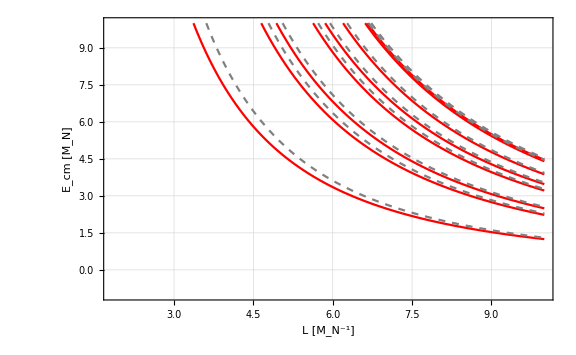

```mathematica
ListPlot[Join[(Transpose@{Llist,(Transpose@spectrum)⟦#⟧})&/@Range[1,levelNum],(Transpose@{Llist,(Transpose@freelines)⟦#⟧})&/@Range[1,freeNum]],Joined->Join[Table[True,{i,1,levelNum}],Table[True,{i,1,freeNum}]],PlotStyle->Join[Table[Directive[Red],{i,1,levelNum}],Table[Directive[Gray,Dashed],{i,1,freeNum}]],Frame->True,GridLines->Automatic,FrameLabel->{"L [M_N^-1]","E_cm [M_N]"},ImageSize->Large,PlotRange->{-1,10}]
```

## C_(2v) - group element (d=(110)) (necessary codes)

```mathematica
(* based on PRD 86, 094513(2012)*)
vecRef={1,1,0};
rotC2v0=rot⟦#⟧&/@{1,18,43,48};
rotC2v=rot⟦#⟧&/@{1,18,43,48,25,42,19,24};
rotC=rotC2v;
```

```mathematica
DeleteDuplicates@(rotC2v0⟦All⟧.vecRef)
DeleteDuplicates@(rotC2v⟦All⟧.vecRef)
```

{{1,1,0}}

{{1,1,0},{-1,-1,0}}

```mathematica
cubicMOV=cubic110;
```

## C_(2v) - group matrix in irreps (d=(110)) (necessary codes)

```mathematica
RA1[i_]:={{1}};
RA1a[i_]:=If[i>Length@rotC2v0,RA1[i-Length@rotC2v0],RA1[i]];
RA1b[i_]:=If[i>Length@rotC2v0,-RA1[i-Length@rotC2v0],RA1[i]];
RA2[i_]:=If[i>2,{{-1}},{{1}}];
RA2a[i_]:=If[i>Length@rotC2v0,RA2[i-Length@rotC2v0],RA2[i]];
RA2b[i_]:=If[i>Length@rotC2v0,-RA2[i-Length@rotC2v0],RA2[i]];

RB1[i_]:=If[i==2||i==4,{{-1}},{{1}}];
RB1a[i_]:=If[i>Length@rotC2v0,RB1[i-Length@rotC2v0],RB1[i]];
RB1b[i_]:=If[i>Length@rotC2v0,-RB1[i-Length@rotC2v0],RB1[i]];
RB2[i_]:=If[i==2||i==3,{{-1}},{{1}}];
RB2a[i_]:=If[i>Length@rotC2v0,RB2[i-Length@rotC2v0],RB2[i]];
RB2b[i_]:=If[i>Length@rotC2v0,-RB2[i-Length@rotC2v0],RB2[i]];


irrepsSet={"A1+","A1-","A2+","A2-","B1+","B1-","B2+","B2-"};
DimIrreps[irreps_]:=1;

GroupMatrix[i_,irreps_]:=If[irreps=="A1+",RA1a[i],If[irreps=="A1-",RA1b[i],If[irreps=="A2+",RA2a[i],If[irreps=="A2-",RA2b[i],If[irreps=="B1+",RB1a[i],If[irreps=="B1-",RB1b[i],If[irreps=="B2+",RB2a[i],RB2b[i]]]]]]]];
```

## C_(2v) - Rebuild the shell data (d=(110))

```mathematica
Hill37=ShellHill[Hill0,37];
```

```mathematica
Hill100=ShellHill[Hill37,100];
```

```mathematica
Hill1k=ShellHill[Hill100,1000];
```

```mathematica
Hill5k=ShellHill[Hill1k,5000];
```

```mathematica
Length@Hill5k
```

27304

```mathematica
Hill5k⟦1⟧
Hill5k⟦2⟧
Hill5k⟦3⟧
Hill5k⟦-1⟧
```

{0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{1,1,4,37,-1,0,0,0,-1,0,0,-1,0,-1,0,0,1,0,0,0,1,0,0,1,0,1,0,0}

{0,1,2,37,0,0,-1,0,0,1,0,0,-1,0,0,1,0,0,1,0,0,-1,0,0,1,0,0,-1}

{17,1350,8,5000,-22,5,-29,5,-22,29,5,-22,-29,-22,5,29,22,-5,29,-5,22,-29,-5,22,29,22,-5,-29}

```mathematica
Hill10k=ShellHill[Hill5k,10000];
```

```mathematica
Length@Hill10k
```

55674

```mathematica
Hill10k⟦1⟧
Hill10k⟦2⟧
Hill10k⟦3⟧
Hill10k⟦-1⟧
```

{0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{1,1,4,37,-1,0,0,0,-1,0,0,-1,0,-1,0,0,1,0,0,0,1,0,0,1,0,1,0,0}

{0,1,2,37,0,0,-1,0,0,1,0,0,-1,0,0,1,0,0,1,0,0,-1,0,0,1,0,0,-1}

{18,2187,8,10000,-29,11,-35,11,-29,35,11,-29,-35,-29,11,35,29,-11,35,-11,29,-35,-11,29,35,29,-11,-35}

```mathematica
(*[|n.d|] [n^2] [# or shell] [run_Index] [nx] [ny] [nz] [nx] [ny] [nz] ... *)
```

```mathematica
Export["cubic_110_expansion_55674.txt",Hill10k,"Table","FieldSeparators"->" "];
```

```mathematica
Export["cubic_110_expansion_27304.txt",Hill5k,"Table","FieldSeparators"->" "];
```

## C_(2v) - Irreps in shell (d=(110))

```mathematica
itest=26;
ptest=cubicMOV⟦itest,#⟧&/@{5,6,7};
Print["reference: ",ptest,". shellnum: ",cubicMOV⟦itest,3⟧];
checknum=0;
For[i=1,i≤Length@irrepsSet,i++,
(*Print[i,"): ",irrepsSet⟦i⟧];*)
resss=ContributeJudgeSum[ptest,irrepsSet⟦i⟧];
If[resss⟦1⟧,{multisss=If[DimIrreps[irrepsSet⟦i⟧]>1,DimIrreps[irrepsSet⟦i⟧]-Count[FullSimplify@Eigenvalues@resss⟦2⟧,0],1];Print[irrepsSet⟦i⟧,": True(",multisss,")."];checknum+=DimIrreps[irrepsSet⟦i⟧]multisss;},{Print[irrepsSet⟦i⟧,": False."]}]
];
If[checknum==cubicMOV⟦itest,3⟧,Print["check OK!"],Print["check num goes wrong!"]];
```

reference: {-2,1,-2}. shellnum: 8

A1+: True(1).

A1-: True(1).

A2+: True(1).

A2-: True(1).

B1+: True(1).

B1-: True(1).

B2+: True(1).

B2-: True(1).

check OK!

```mathematica
irrepsContribute[itest,#]&/@irrepsSet
```

{True,True,True,True,True,True,True,True}

## C_(2v) - Projection (d=(110)) (necessary codes)

```mathematica
V[p_,q_]:=Vg[p,q];mNp=mN;
```

```mathematica
L=2π;prec=16;prnt=1;
EmatrixProjection[1,5,"A1+"]//MatrixForm
VmatrixProjection[1,5,"A1+"]//FullSimplify//MatrixForm
levels0=EnergyLevelsProjection0[1,5,"A1+"];
Print["-----------------------------------"];
fakes=EnergyLevelsProjectionFree[1,5,"A1+"];
Print["-----------------------------------"];
levels=DeleteFakePole[levels0,fakes];
```

(1/2 | 0 | 0 | 0 | 0
0 | 5/2 | 0 | 0 | 0
0 | 0 | 3/2 | 0 | 0
0 | 0 | 0 | 9/2 | 0
0 | 0 | 0 | 0 | 7/2)

(45792289/(48000000 π^3) | 45792289/(1101360000 π^3) | 45792289/(1101360000 √2 π^3) | 45792289/(2178720000 √2 π^3) | 45792289/(1089360000 √2 π^3)
45792289/(1101360000 π^3) | 964107235015169/(983474208000000 π^3) | 45792289/(1089360000 √2 π^3) | 621263984863/(12415080600000 √2 π^3) | 6583156569624383/(84217699250100000 √2 π^3)
45792289/(1101360000 √2 π^3) | 45792289/(1089360000 √2 π^3) | 69283733257/(72224000000 π^3) | 45792289/(3256080000 π^3) | 621263984863/(12415080600000 π^3)
45792289/(2178720000 √2 π^3) | 621263984863/(12415080600000 √2 π^3) | 45792289/(3256080000 π^3) | 103353196273/(108036000000 π^3) | 103353196273/(3681219780000 π^3)
45792289/(1089360000 √2 π^3) | 6583156569624383/(84217699250100000 √2 π^3) | 621263984863/(12415080600000 π^3) | 103353196273/(3681219780000 π^3) | 19853289892211793047299/(19947078114738768000000 π^3))

0.530766000091119

1.53093717176042

2.53161440788963

3.5321038557448

4.53085519790289

-----------------------------------

0.5

1.5

2.5

3.5

4.5

-----------------------------------

0.530766000091119

1.53093717176042

2.53161440788963

3.5321038557448

4.53085519790289

```mathematica
L=2π;prec=16;prnt=1;
(*EmatrixProjection[1,5,"A1+"]//MatrixForm
VmatrixProjection[1,5,"A1+"]//MatrixForm*)
levels0=EnergyLevelsProjection0[1,15,"A1+"];
Print["-----------------------------------"];
fakes=EnergyLevelsProjectionFree[1,15,"A1+"];
Print["-----------------------------------"];
levels=DeleteFakePole[levels0,fakes];
```

0.530765665188119

1.53093621473582

2.53003151941685

2.53243229439471

3.53006154930514

3.53312150539451

4.53060321738646

4.53106103265055

5.5310818828198

6.53017147203343

6.53122866048091

6.53253210208403

7.53130337169196

8.53117934080653

9.5315270815367

-----------------------------------

0.5

1.5

2.5

2.5

3.5

3.5

4.5

4.5

5.5

6.5

6.5

6.5

7.5

8.5

9.5

-----------------------------------

0.530765665188119

1.53093621473582

2.53003151941685

2.53243229439471

3.53006154930514

3.53312150539451

4.53060321738646

4.53106103265055

5.5310818828198

6.53017147203343

6.53122866048091

6.53253210208403

7.53130337169196

8.53117934080653

9.5315270815367

```mathematica
L=2π;prec=16;prnt=1;
EmatrixProjection[1,5,"B1+"]//MatrixForm
VmatrixProjection[1,5,"B1+"]//FullSimplify//MatrixForm
levels0=EnergyLevelsProjection0[1,5,"B1+"];
Print["-----------------------------------"];
fakes=EnergyLevelsProjectionFree[1,5,"B1+"];
Print["-----------------------------------"];
levels=DeleteFakePole[levels0,fakes];
```

(7/2)

(922765956505969/(975349008000000 π^3))

3.53051278852589

-----------------------------------

3.5

-----------------------------------

3.53051278852589

```mathematica
L=2π;prec=16;prnt=1;
(*EmatrixProjection[1,15,"E+"]//MatrixForm
VmatrixProjection[1,15,"E+"]//FullSimplify//MatrixForm*)
levels0=EnergyLevelsProjection0[1,15,"B2-"];
Print["-----------------------------------"];
fakes=EnergyLevelsProjectionFree[1,15,"B2-"];
Print["-----------------------------------"];
levels=DeleteFakePole[levels0,fakes];
```

2.52988369178945

2.5313946833507

3.52989683682777

3.53158311331242

6.53014911138707

6.53057622404255

6.53164053803889

7.53086262623437

8.530432909102

9.5304928601939

-----------------------------------

2.5

2.5

3.5

3.5

6.5

6.5

6.5

7.5

8.5

9.5

-----------------------------------

2.52988369178945

2.5313946833507

3.52989683682777

3.53158311331242

6.53014911138707

6.53057622404255

6.53164053803889

7.53086262623437

8.530432909102

9.5304928601939

## Spectrum (d=(110))

### V_SF and m_N=m'_N

```mathematica
V[p_,q_]:=VSF[p,q];mNp=mN;
```

#### A_1^+

```mathematica
prec=16;pcut=40;prnt=0;irreps="A1+";levelNum=18;
L=2π;
freeNum=ShellAnalysis[1,pcut,irreps,levelNum];
```

1): {0,0,0} --> A1+ x 1. ω = 0.5

2): {-1,0,0} --> A1+ x 1. ω = 2.5

3): {0,0,-1} --> A1+ x 1. ω = 1.5

4): {-1,-1,0} --> A1+ x 1. ω = 4.5

5): {-1,0,-1} --> A1+ x 1. ω = 3.5

6): {-1,1,0} --> A1+ x 1. ω = 2.5

7): {-1,-1,-1} --> A1+ x 1. ω = 5.5

8): {-1,1,-1} --> A1+ x 1. ω = 3.5

9): {-2,0,0} --> A1+ x 1. ω = 6.5

10): {0,0,-2} --> A1+ x 1. ω = 4.5

11): {-2,-1,0} --> A1+ x 1. ω = 8.5

12): {-2,0,-1} --> A1+ x 1. ω = 7.5

13): {-2,1,0} --> A1+ x 1. ω = 6.5

14): {-1,0,-2} --> A1+ x 1. ω = 6.5

15): {-2,-1,-1} --> A1+ x 1. ω = 9.5

16): {-2,1,-1} --> A1+ x 1. ω = 7.5

17): {-1,-1,-2} --> A1+ x 1. ω = 8.5

18): {-1,1,-2} --> A1+ x 1. ω = 6.5

19): {-2,-2,0} --> A1+ x 1. ω = 12.5

```mathematica
prec=16;pcut=20;prnt=0;irreps="A1+";levelNum=8;
freelines={};spectrum={};
Llist=Range[2,10,8/100];
For[j=1,j≤Length@Llist,j++,L=Llist⟦j⟧;
levels0=EnergyLevelsProjection0[1,pcut,irreps];
(*Print["-----------------------------------"];*)
fakes=EnergyLevelsProjectionFree[1,pcut,irreps];
(*Print["-----------------------------------"];*)
levels=DeleteFakePole[levels0,fakes];
fakesTruncated=Table[fakes⟦i⟧,{i,1,levelNum}];
levelsTruncated=Table[levels⟦i⟧,{i,1,levelNum}];
AppendTo[freelines,fakesTruncated];
AppendTo[spectrum,levelsTruncated];
Print[j,"): L = ",N@L];
]
```

1): L = 2.

2): L = 2.08

3): L = 2.16

4): L = 2.24

5): L = 2.32

6): L = 2.4

7): L = 2.48

8): L = 2.56

9): L = 2.64

10): L = 2.72

11): L = 2.8

12): L = 2.88

13): L = 2.96

14): L = 3.04

15): L = 3.12

16): L = 3.2

17): L = 3.28

18): L = 3.36

19): L = 3.44

20): L = 3.52

21): L = 3.6

22): L = 3.68

23): L = 3.76

24): L = 3.84

25): L = 3.92

26): L = 4.

27): L = 4.08

28): L = 4.16

29): L = 4.24

30): L = 4.32

31): L = 4.4

32): L = 4.48

33): L = 4.56

34): L = 4.64

35): L = 4.72

36): L = 4.8

37): L = 4.88

38): L = 4.96

39): L = 5.04

40): L = 5.12

41): L = 5.2

42): L = 5.28

43): L = 5.36

44): L = 5.44

45): L = 5.52

46): L = 5.6

47): L = 5.68

48): L = 5.76

49): L = 5.84

50): L = 5.92

51): L = 6.

52): L = 6.08

53): L = 6.16

54): L = 6.24

55): L = 6.32

56): L = 6.4

57): L = 6.48

58): L = 6.56

59): L = 6.64

60): L = 6.72

61): L = 6.8

62): L = 6.88

63): L = 6.96

64): L = 7.04

65): L = 7.12

66): L = 7.2

67): L = 7.28

68): L = 7.36

69): L = 7.44

70): L = 7.52

71): L = 7.6

72): L = 7.68

73): L = 7.76

74): L = 7.84

75): L = 7.92

76): L = 8.

77): L = 8.08

78): L = 8.16

79): L = 8.24

80): L = 8.32

81): L = 8.4

82): L = 8.48

83): L = 8.56

84): L = 8.64

85): L = 8.72

86): L = 8.8

87): L = 8.88

88): L = 8.96

89): L = 9.04

90): L = 9.12

91): L = 9.2

92): L = 9.28

93): L = 9.36

94): L = 9.44

95): L = 9.52

96): L = 9.6

97): L = 9.68

98): L = 9.76

99): L = 9.84

100): L = 9.92

101): L = 10.

```mathematica
dataFree=Transpose@Join[{N@Llist},Transpose@freelines];
dataSpectrum=Transpose@Join[{N@Llist},Transpose@spectrum];
Export["freelines_A1+_110.txt",dataFree,"Table","FieldSeparators"->" "];
Export["spectra_A1+_110.txt",dataSpectrum,"Table","FieldSeparators"->" "];
```

```mathematica
dataFree0=Import["freelines_A1+_110.txt","Table","FieldSeparators"->" "];
dataSpectrum0=Import["spectra_A1+_110.txt","Table","FieldSeparators"->" "];
plotFree=(Transpose@{(Transpose@dataFree0)⟦1⟧,(Transpose@dataFree0)⟦#⟧})&/@Range[2,levelNum+1];
plotSpectrum=(Transpose@{(Transpose@dataSpectrum0)⟦1⟧,(Transpose@dataSpectrum0)⟦#⟧})&/@Range[2,levelNum+1];
```

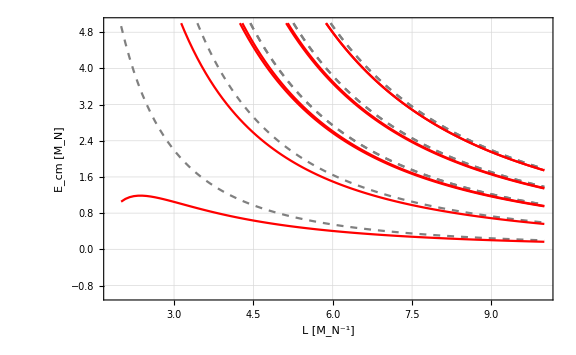

```mathematica
plotsave=ListPlot[Join[plotFree,plotSpectrum],Joined->Join[Table[True,{i,1,levelNum}],Table[True,{i,1,levelNum}]],PlotStyle->Join[Table[Directive[Gray,Dashed],{i,1,levelNum}],Table[Directive[Red],{i,1,levelNum}]],Frame->True,GridLines->Automatic,FrameLabel->{"L [M_N^-1]","E_cm [M_N]"},ImageSize->Large,PlotRange->{-1,5}]
```

```mathematica
Export["spectrum_A1+_110.pdf",plotsave];
```

#### B_2^- (not done)

```mathematica
prec=16;pcut=30;prnt=0;irreps="B2-";levelNum=8;
L=2π;
freeNum=ShellAnalysis[1,pcut,irreps,levelNum];
```

6): {-1,-1,-1} --> B2- x 1. ω = 4.25

12): {-2,-1,-1} --> B2- x 1. ω = 7.25

13): {-1,-1,-2} --> B2- x 1. ω = 8.25

18): {-2,-2,-1} --> B2- x 1. ω = 10.25

19): {-2,-1,-2} --> B2- x 1. ω = 11.25

23): {-3,-1,-1} --> B2- x 1. ω = 12.25

24): {-1,-1,-3} --> B2- x 1. ω = 14.25

25): {-2,-2,-2} --> B2- x 1. ω = 14.25

29): {-3,-2,-1} --> B2- x 1. ω = 15.25

```mathematica
prec=16;pcut=30;prnt=0;irreps="B2-";levelNum=8;
freelines={};spectrum={};
Llist=Range[2,10,8/100];
For[j=1,j≤Length@Llist,j++,L=Llist⟦j⟧;
levels0=EnergyLevelsProjection0[1,pcut,irreps];
(*Print["-----------------------------------"];*)
fakes=EnergyLevelsProjectionFree[1,pcut,irreps];
(*Print["-----------------------------------"];*)
levels=DeleteFakePole[levels0,fakes];
fakesTruncated=Table[fakes⟦i⟧,{i,1,levelNum}];
levelsTruncated=Table[levels⟦i⟧,{i,1,levelNum}];
AppendTo[freelines,fakesTruncated];
AppendTo[spectrum,levelsTruncated];
Print[j,"): L = ",N@L];
]
```

1): L = 2.

2): L = 2.08

3): L = 2.16

4): L = 2.24

5): L = 2.32

6): L = 2.4

7): L = 2.48

8): L = 2.56

9): L = 2.64

10): L = 2.72

11): L = 2.8

12): L = 2.88

13): L = 2.96

14): L = 3.04

15): L = 3.12

16): L = 3.2

17): L = 3.28

18): L = 3.36

19): L = 3.44

20): L = 3.52

21): L = 3.6

22): L = 3.68

23): L = 3.76

24): L = 3.84

25): L = 3.92

26): L = 4.

27): L = 4.08

28): L = 4.16

29): L = 4.24

30): L = 4.32

31): L = 4.4

32): L = 4.48

33): L = 4.56

34): L = 4.64

35): L = 4.72

36): L = 4.8

37): L = 4.88

38): L = 4.96

39): L = 5.04

40): L = 5.12

41): L = 5.2

42): L = 5.28

43): L = 5.36

44): L = 5.44

45): L = 5.52

46): L = 5.6

47): L = 5.68

48): L = 5.76

49): L = 5.84

50): L = 5.92

51): L = 6.

52): L = 6.08

53): L = 6.16

54): L = 6.24

55): L = 6.32

56): L = 6.4

57): L = 6.48

58): L = 6.56

59): L = 6.64

60): L = 6.72

61): L = 6.8

62): L = 6.88

63): L = 6.96

64): L = 7.04

65): L = 7.12

66): L = 7.2

67): L = 7.28

68): L = 7.36

69): L = 7.44

70): L = 7.52

71): L = 7.6

72): L = 7.68

73): L = 7.76

74): L = 7.84

75): L = 7.92

76): L = 8.

77): L = 8.08

78): L = 8.16

79): L = 8.24

80): L = 8.32

81): L = 8.4

82): L = 8.48

83): L = 8.56

84): L = 8.64

85): L = 8.72

86): L = 8.8

87): L = 8.88

88): L = 8.96

89): L = 9.04

90): L = 9.12

91): L = 9.2

92): L = 9.28

93): L = 9.36

94): L = 9.44

95): L = 9.52

96): L = 9.6

97): L = 9.68

98): L = 9.76

99): L = 9.84

100): L = 9.92

101): L = 10.

```mathematica
prec=16;pcut=30;prnt=0;irreps="B2-";levelNum=8;
freelines={};
Llist=Range[2,10,8/100];
For[j=1,j≤Length@Llist,j++,L=Llist⟦j⟧;
(*Print["-----------------------------------"];*)
fakes=EnergyLevelsProjectionFree[1,pcut,irreps];
(*Print["-----------------------------------"];*)
equalPrecision[x1_,x2_]:=(Abs@(x1-x2)≤10^-9);
fakes=DeleteDuplicates[fakes,equalPrecision];
fakesTruncated=Table[fakes⟦i⟧,{i,1,freeNum}];

AppendTo[freelines,fakesTruncated];

Print[j,"): L = ",N@L];
]
```

1): L = 2.

2): L = 2.08

3): L = 2.16

4): L = 2.24

5): L = 2.32

6): L = 2.4

7): L = 2.48

8): L = 2.56

9): L = 2.64

10): L = 2.72

11): L = 2.8

12): L = 2.88

13): L = 2.96

14): L = 3.04

15): L = 3.12

16): L = 3.2

17): L = 3.28

18): L = 3.36

19): L = 3.44

20): L = 3.52

21): L = 3.6

22): L = 3.68

23): L = 3.76

24): L = 3.84

25): L = 3.92

26): L = 4.

27): L = 4.08

28): L = 4.16

29): L = 4.24

30): L = 4.32

31): L = 4.4

32): L = 4.48

33): L = 4.56

34): L = 4.64

35): L = 4.72

36): L = 4.8

37): L = 4.88

38): L = 4.96

39): L = 5.04

40): L = 5.12

41): L = 5.2

42): L = 5.28

43): L = 5.36

44): L = 5.44

45): L = 5.52

46): L = 5.6

47): L = 5.68

48): L = 5.76

49): L = 5.84

50): L = 5.92

51): L = 6.

52): L = 6.08

53): L = 6.16

54): L = 6.24

55): L = 6.32

56): L = 6.4

57): L = 6.48

58): L = 6.56

59): L = 6.64

60): L = 6.72

61): L = 6.8

62): L = 6.88

63): L = 6.96

64): L = 7.04

65): L = 7.12

66): L = 7.2

67): L = 7.28

68): L = 7.36

69): L = 7.44

70): L = 7.52

71): L = 7.6

72): L = 7.68

73): L = 7.76

74): L = 7.84

75): L = 7.92

76): L = 8.

77): L = 8.08

78): L = 8.16

79): L = 8.24

80): L = 8.32

81): L = 8.4

82): L = 8.48

83): L = 8.56

84): L = 8.64

85): L = 8.72

86): L = 8.8

87): L = 8.88

88): L = 8.96

89): L = 9.04

90): L = 9.12

91): L = 9.2

92): L = 9.28

93): L = 9.36

94): L = 9.44

95): L = 9.52

96): L = 9.6

97): L = 9.68

98): L = 9.76

99): L = 9.84

100): L = 9.92

101): L = 10.

```mathematica
ListPlot[Join[(Transpose@{Llist,(Transpose@spectrum)⟦#⟧})&/@Range[1,levelNum],(Transpose@{Llist,(Transpose@freelines)⟦#⟧})&/@Range[1,freeNum]],Joined->Join[Table[True,{i,1,levelNum}],Table[True,{i,1,freeNum}]],PlotStyle->Join[Table[Directive[Red],{i,1,levelNum}],Table[Directive[Gray,Dashed],{i,1,freeNum}]],Frame->True,GridLines->Automatic,FrameLabel->{"L [M_N^-1]","E_cm [M_N]"},ImageSize->Large,PlotRange->{-1,10}]
```

-Graphics-

### V_SF and m_N≠m'_N

```mathematica
V[p_,q_]:=VSF[p,q];mNp=5/√11;
```

#### A_1^+

```mathematica
prec=16;pcut=40;prnt=0;irreps="A1+";levelNum=18;
L=2π;
freeNum=ShellAnalysis[1,pcut,irreps,levelNum];
```

1): {0,0,0} --> A1+ x 1. ω = 0.26453

2): {-1,0,0} --> A1+ x 1. ω = 1.75952

3): {0,0,-1} --> A1+ x 1. ω = 1.09619

4): {-1,-1,0} --> A1+ x 1. ω = 3.25451

5): {-1,0,-1} --> A1+ x 1. ω = 2.59118

6): {-1,1,0} --> A1+ x 1. ω = 1.92786

7): {-1,-1,-1} --> A1+ x 1. ω = 4.08617

8): {-1,1,-1} --> A1+ x 1. ω = 2.75952

9): {-2,0,0} --> A1+ x 1. ω = 4.91783

10): {0,0,-2} --> A1+ x 1. ω = 3.59118

11): {-2,-1,0} --> A1+ x 1. ω = 6.41282

12): {-2,0,-1} --> A1+ x 1. ω = 5.74949

13): {-2,1,0} --> A1+ x 1. ω = 5.08617

14): {-1,0,-2} --> A1+ x 1. ω = 5.08617

15): {-2,-1,-1} --> A1+ x 1. ω = 7.24448

16): {-2,1,-1} --> A1+ x 1. ω = 5.91783

17): {-1,-1,-2} --> A1+ x 1. ω = 6.58116

18): {-1,1,-2} --> A1+ x 1. ω = 5.25451

19): {-2,-2,0} --> A1+ x 1. ω = 9.57113

```mathematica
prec=16;pcut=20;prnt=0;irreps="A1+";levelNum=8;
freelines={};spectrum={};
Llist=Range[2,10,8/100];
For[j=1,j≤Length@Llist,j++,L=Llist⟦j⟧;
levels0=EnergyLevelsProjection0[1,pcut,irreps];
(*Print["-----------------------------------"];*)
fakes=EnergyLevelsProjectionFree[1,pcut,irreps];
(*Print["-----------------------------------"];*)
levels=DeleteFakePole[levels0,fakes];
fakesTruncated=Table[fakes⟦i⟧,{i,1,levelNum}];
levelsTruncated=Table[levels⟦i⟧,{i,1,levelNum}];
AppendTo[freelines,fakesTruncated];
AppendTo[spectrum,levelsTruncated];
Print[j,"): L = ",N@L];
]
```

1): L = 2.

2): L = 2.08

3): L = 2.16

4): L = 2.24

5): L = 2.32

6): L = 2.4

7): L = 2.48

8): L = 2.56

9): L = 2.64

10): L = 2.72

11): L = 2.8

12): L = 2.88

13): L = 2.96

14): L = 3.04

15): L = 3.12

16): L = 3.2

17): L = 3.28

18): L = 3.36

19): L = 3.44

20): L = 3.52

21): L = 3.6

22): L = 3.68

23): L = 3.76

24): L = 3.84

25): L = 3.92

26): L = 4.

27): L = 4.08

28): L = 4.16

29): L = 4.24

30): L = 4.32

31): L = 4.4

32): L = 4.48

33): L = 4.56

34): L = 4.64

35): L = 4.72

36): L = 4.8

37): L = 4.88

38): L = 4.96

39): L = 5.04

40): L = 5.12

41): L = 5.2

42): L = 5.28

43): L = 5.36

44): L = 5.44

45): L = 5.52

46): L = 5.6

47): L = 5.68

48): L = 5.76

49): L = 5.84

50): L = 5.92

51): L = 6.

52): L = 6.08

53): L = 6.16

54): L = 6.24

55): L = 6.32

56): L = 6.4

57): L = 6.48

58): L = 6.56

59): L = 6.64

60): L = 6.72

61): L = 6.8

62): L = 6.88

63): L = 6.96

64): L = 7.04

65): L = 7.12

66): L = 7.2

67): L = 7.28

68): L = 7.36

69): L = 7.44

70): L = 7.52

71): L = 7.6

72): L = 7.68

73): L = 7.76

74): L = 7.84

75): L = 7.92

76): L = 8.

77): L = 8.08

78): L = 8.16

79): L = 8.24

80): L = 8.32

81): L = 8.4

82): L = 8.48

83): L = 8.56

84): L = 8.64

85): L = 8.72

86): L = 8.8

87): L = 8.88

88): L = 8.96

89): L = 9.04

90): L = 9.12

91): L = 9.2

92): L = 9.28

93): L = 9.36

94): L = 9.44

95): L = 9.52

96): L = 9.6

97): L = 9.68

98): L = 9.76

99): L = 9.84

100): L = 9.92

101): L = 10.

```mathematica
dataFree=Transpose@Join[{N@Llist},Transpose@freelines];
dataSpectrum=Transpose@Join[{N@Llist},Transpose@spectrum];
Export["freelines_A1+_110_2.txt",dataFree,"Table","FieldSeparators"->" "];
Export["spectra_A1+_110_2.txt",dataSpectrum,"Table","FieldSeparators"->" "];
```

```mathematica
dataFree0=Import["freelines_A1+_110_2.txt","Table","FieldSeparators"->" "];
dataSpectrum0=Import["spectra_A1+_110_2.txt","Table","FieldSeparators"->" "];
plotFree=(Transpose@{(Transpose@dataFree0)⟦1⟧,(Transpose@dataFree0)⟦#⟧})&/@Range[2,levelNum+1];
plotSpectrum=(Transpose@{(Transpose@dataSpectrum0)⟦1⟧,(Transpose@dataSpectrum0)⟦#⟧})&/@Range[2,levelNum+1];
```

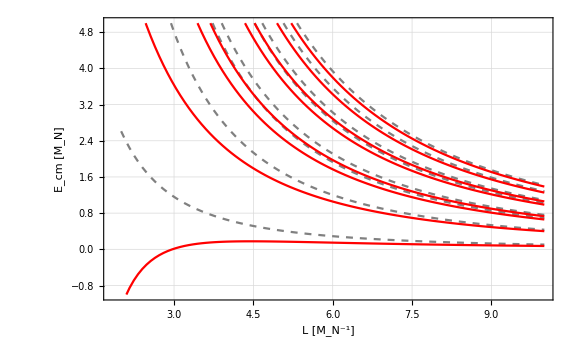

```mathematica
plotsave=ListPlot[Join[plotFree,plotSpectrum],Joined->Join[Table[True,{i,1,levelNum}],Table[True,{i,1,levelNum}]],PlotStyle->Join[Table[Directive[Gray,Dashed],{i,1,levelNum}],Table[Directive[Red],{i,1,levelNum}]],Frame->True,GridLines->Automatic,FrameLabel->{"L [M_N^-1]","E_cm [M_N]"},ImageSize->Large,PlotRange->{-1,5}]
```

```mathematica
Export["spectrum_A1+_110_2.pdf",plotsave];
```

#### B_2^-

```mathematica
prec=16;pcut=30;prnt=0;irreps="B2-";levelNum=8;
L=2π;
freeNum=ShellAnalysis[1,pcut,irreps,levelNum];
```

6): {-1,-1,-1} --> B2- x 1. ω = 3.3

12): {-2,-1,-1} --> B2- x 1. ω = 5.8

13): {-1,-1,-2} --> B2- x 1. ω = 6.46667

18): {-2,-2,-1} --> B2- x 1. ω = 8.3

19): {-2,-1,-2} --> B2- x 1. ω = 8.96667

23): {-3,-1,-1} --> B2- x 1. ω = 9.96667

24): {-1,-1,-3} --> B2- x 1. ω = 11.3

25): {-2,-2,-2} --> B2- x 1. ω = 11.4667

29): {-3,-2,-1} --> B2- x 1. ω = 12.4667

```mathematica
prec=16;pcut=30;prnt=0;irreps="B2-";levelNum=8;
freelines={};spectrum={};
Llist=Range[2,10,8/100];
For[j=1,j≤Length@Llist,j++,L=Llist⟦j⟧;
levels0=EnergyLevelsProjection0[1,pcut,irreps];
(*Print["-----------------------------------"];*)
fakes=EnergyLevelsProjectionFree[1,pcut,irreps];
(*Print["-----------------------------------"];*)
levels=DeleteFakePole[levels0,fakes];
fakesTruncated=Table[fakes⟦i⟧,{i,1,levelNum}];
levelsTruncated=Table[levels⟦i⟧,{i,1,levelNum}];
AppendTo[freelines,fakesTruncated];
AppendTo[spectrum,levelsTruncated];
Print[j,"): L = ",N@L];
]
```

1): L = 2.

2): L = 2.08

3): L = 2.16

4): L = 2.24

5): L = 2.32

6): L = 2.4

7): L = 2.48

8): L = 2.56

9): L = 2.64

10): L = 2.72

11): L = 2.8

12): L = 2.88

13): L = 2.96

14): L = 3.04

15): L = 3.12

16): L = 3.2

17): L = 3.28

18): L = 3.36

19): L = 3.44

20): L = 3.52

21): L = 3.6

22): L = 3.68

23): L = 3.76

24): L = 3.84

25): L = 3.92

26): L = 4.

27): L = 4.08

28): L = 4.16

29): L = 4.24

30): L = 4.32

31): L = 4.4

32): L = 4.48

33): L = 4.56

34): L = 4.64

35): L = 4.72

36): L = 4.8

37): L = 4.88

38): L = 4.96

39): L = 5.04

40): L = 5.12

41): L = 5.2

42): L = 5.28

43): L = 5.36

44): L = 5.44

45): L = 5.52

46): L = 5.6

47): L = 5.68

48): L = 5.76

49): L = 5.84

50): L = 5.92

51): L = 6.

52): L = 6.08

53): L = 6.16

54): L = 6.24

55): L = 6.32

56): L = 6.4

57): L = 6.48

58): L = 6.56

59): L = 6.64

60): L = 6.72

61): L = 6.8

62): L = 6.88

63): L = 6.96

64): L = 7.04

65): L = 7.12

66): L = 7.2

67): L = 7.28

68): L = 7.36

69): L = 7.44

70): L = 7.52

71): L = 7.6

72): L = 7.68

73): L = 7.76

74): L = 7.84

75): L = 7.92

76): L = 8.

77): L = 8.08

78): L = 8.16

79): L = 8.24

80): L = 8.32

81): L = 8.4

82): L = 8.48

83): L = 8.56

84): L = 8.64

85): L = 8.72

86): L = 8.8

87): L = 8.88

88): L = 8.96

89): L = 9.04

90): L = 9.12

91): L = 9.2

92): L = 9.28

93): L = 9.36

94): L = 9.44

95): L = 9.52

96): L = 9.6

97): L = 9.68

98): L = 9.76

99): L = 9.84

100): L = 9.92

101): L = 10.

```mathematica
prec=16;pcut=30;prnt=0;irreps="B2-";levelNum=8;
freelines={};
Llist=Range[2,10,8/100];
For[j=1,j≤Length@Llist,j++,L=Llist⟦j⟧;
(*Print["-----------------------------------"];*)
fakes=EnergyLevelsProjectionFree[1,pcut,irreps];
(*Print["-----------------------------------"];*)
equalPrecision[x1_,x2_]:=(Abs@(x1-x2)≤10^-9);
fakes=DeleteDuplicates[fakes,equalPrecision];
fakesTruncated=Table[fakes⟦i⟧,{i,1,freeNum}];

AppendTo[freelines,fakesTruncated];

Print[j,"): L = ",N@L];
]
```

1): L = 2.

2): L = 2.08

3): L = 2.16

4): L = 2.24

5): L = 2.32

6): L = 2.4

7): L = 2.48

8): L = 2.56

9): L = 2.64

10): L = 2.72

11): L = 2.8

12): L = 2.88

13): L = 2.96

14): L = 3.04

15): L = 3.12

16): L = 3.2

17): L = 3.28

18): L = 3.36

19): L = 3.44

20): L = 3.52

21): L = 3.6

22): L = 3.68

23): L = 3.76

24): L = 3.84

25): L = 3.92

26): L = 4.

27): L = 4.08

28): L = 4.16

29): L = 4.24

30): L = 4.32

31): L = 4.4

32): L = 4.48

33): L = 4.56

34): L = 4.64

35): L = 4.72

36): L = 4.8

37): L = 4.88

38): L = 4.96

39): L = 5.04

40): L = 5.12

41): L = 5.2

42): L = 5.28

43): L = 5.36

44): L = 5.44

45): L = 5.52

46): L = 5.6

47): L = 5.68

48): L = 5.76

49): L = 5.84

50): L = 5.92

51): L = 6.

52): L = 6.08

53): L = 6.16

54): L = 6.24

55): L = 6.32

56): L = 6.4

57): L = 6.48

58): L = 6.56

59): L = 6.64

60): L = 6.72

61): L = 6.8

62): L = 6.88

63): L = 6.96

64): L = 7.04

65): L = 7.12

66): L = 7.2

67): L = 7.28

68): L = 7.36

69): L = 7.44

70): L = 7.52

71): L = 7.6

72): L = 7.68

73): L = 7.76

74): L = 7.84

75): L = 7.92

76): L = 8.

77): L = 8.08

78): L = 8.16

79): L = 8.24

80): L = 8.32

81): L = 8.4

82): L = 8.48

83): L = 8.56

84): L = 8.64

85): L = 8.72

86): L = 8.8

87): L = 8.88

88): L = 8.96

89): L = 9.04

90): L = 9.12

91): L = 9.2

92): L = 9.28

93): L = 9.36

94): L = 9.44

95): L = 9.52

96): L = 9.6

97): L = 9.68

98): L = 9.76

99): L = 9.84

100): L = 9.92

101): L = 10.

```mathematica
ListPlot[Join[(Transpose@{Llist,(Transpose@spectrum)⟦#⟧})&/@Range[1,levelNum],(Transpose@{Llist,(Transpose@freelines)⟦#⟧})&/@Range[1,freeNum]],Joined->Join[Table[True,{i,1,levelNum}],Table[True,{i,1,freeNum}]],PlotStyle->Join[Table[Directive[Red],{i,1,levelNum}],Table[Directive[Gray,Dashed],{i,1,freeNum}]],Frame->True,GridLines->Automatic,FrameLabel->{"L [M_N^-1]","E_cm [M_N]"},ImageSize->Large,PlotRange->{-1,10}]
```

-Graphics-